# Linear Chiral (E_1'=k_B θ+eV_g,E_2'=k_B θ+eV_g)(Voltage temperature probe)

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T12uu=TX TY;
T13uu=TX (1-TY);
T21uu=0;
T22uu=(1-TY);
T23uu=TY;
T31uu=TX;
T32uu=TY(1-TX);
T33uu=(1-TX)( 1-TY);
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
V=0.43;
Vg=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(1-T11uu)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G12=NIntegrate[(-T12uu)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G13=NIntegrate[(-T13uu)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G31=NIntegrate[(-T31uu)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G32=NIntegrate[(-T32uu)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G33=NIntegrate[(1-T33uu)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L11=NIntegrate[(1-T11uu)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L12=NIntegrate[(-T12uu)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L13=NIntegrate[(-T13uu)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L23=NIntegrate[(-T23uu)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L33=NIntegrate[(1-T33uu)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L31=NIntegrate[(-T31uu)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L32=NIntegrate[(-T32uu)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π11=NIntegrate[(1-T11uu)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π12=NIntegrate[(-T12uu)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π13=NIntegrate[(-T13uu)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π31=NIntegrate[(-T31uu)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π33=NIntegrate[(1-T33uu)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K11=NIntegrate[(1-T11uu)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K12=NIntegrate[(-T12uu)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K13=NIntegrate[(-T13uu)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K31=NIntegrate[(-T31uu)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K32=NIntegrate[(-T32uu)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K33=NIntegrate[(1-T33uu)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z}];
},{x1,44,85,1}];//AbsoluteTiming
list=Sort[list1];
Export["check20.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 100 recursive bisections in G near {G} = {1.}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 100 recursive bisections in G near {G} = {1.}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 100 recursive bisections in G near {G} = {1.}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 100 recursive bisections in G near {G} = {1.}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{11.5981,Null}

check20.dat

# Linear Helical (E_1'=k_B θ+eV_g,E_2'=k_B θ+eV_g)(Voltage-temperature probe)

```mathematica
kb=1;
T=1;
θ=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=x1*a/ec;
V=0.43*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z,Jq*h/(kb^2*θ*δT),Subscript[η, r]}]
},{x1,44,85,1}];//AbsoluteTiming
list=Sort[list1];
Export["check40.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {52.4935}. NIntegrate obtained 1.92135×10^-23 and 1.02755×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {55.7216}. NIntegrate obtained 9.57635×10^-25 and 4.70669×10^-27 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {61.31}. NIntegrate obtained 2.3711×10^-27 and 4.99841×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {64.876}. NIntegrate obtained 1.18155×10^-28 and 3.48723×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {43.8983}. NIntegrate obtained 1.55693×10^-19 and 1.17689×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {46.9912}. NIntegrate obtained 7.7512×10^-21 and 1.00146×10^-23 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {49.5985}. NIntegrate obtained 3.85991×10^-22 and 1.33849×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {52.4935}. NIntegrate obtained -9.4535×10^-24 and 1.90329×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {55.7216}. NIntegrate obtained -4.68711×10^-25 and 9.77127×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {58.7049}. NIntegrate obtained 4.78809×10^-26 and 9.55907×10^-28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {61.9944}. NIntegrate obtained -1.16532×10^-27 and 2.39624×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {64.876}. NIntegrate obtained -5.84381×10^-29 and 1.78591×10^-30 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {52.4935}. NIntegrate obtained -9.76001×10^-24 and 2.92582×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {61.31}. NIntegrate obtained -1.21085×10^-27 and 3.97708×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {64.876}. NIntegrate obtained -5.9717×10^-29 and 1.70132×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {43.8983}. NIntegrate obtained -7.66528×10^-20 and 6.20154×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {46.9912}. NIntegrate obtained -3.81404×10^-21 and 1.36571×10^-23 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {49.5985}. NIntegrate obtained -1.89859×10^-22 and 6.21958×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {55.7216}. NIntegrate obtained -4.88924×10^-25 and 1.44278×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {58.7049}. NIntegrate obtained -2.3486×10^-26 and 6.66067×10^-29 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {43.8983}. NIntegrate obtained -7.90399×10^-20 and 5.56739×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {46.5819}. NIntegrate obtained -3.93724×10^-21 and 1.29438×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {49.5985}. NIntegrate obtained -1.96132×10^-22 and 1.91885×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {58.7049}. NIntegrate obtained -2.43948×10^-26 and 8.893×10^-28 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {68.0079}. NIntegrate obtained 5.81028×10^-30 and 2.05298×10^-32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {70.5393}. NIntegrate obtained 2.8786×10^-31 and 1.25625×10^-32 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {79.2334}. NIntegrate obtained 3.64223×10^-35 and 3.06795×10^-36 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 6.49312×10^-37 and 2.28068×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {68.0079}. NIntegrate obtained -2.88211×10^-30 and 1.12051×10^-32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {70.5393}. NIntegrate obtained -1.41686×10^-31 and 8.45717×10^-33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {73.2429}. NIntegrate obtained 1.44492×10^-32 and 5.86072×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {75.1489}. NIntegrate obtained 1.98118×10^-33 and 3.19607×10^-35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {77.1438}. NIntegrate obtained 2.68168×10^-34 and 1.33831×10^-35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {79.2334}. NIntegrate obtained -1.81309×10^-35 and 1.48103×10^-36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {81.4236}. NIntegrate obtained 4.76657×10^-36 and 2.18012×10^-37 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {67.1999}. NIntegrate obtained -2.99254×10^-30 and 9.56774×10^-33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {70.5393}. NIntegrate obtained -1.46174×10^-31 and 4.10537×10^-33 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -3.15219×10^-37 and 2.06789×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {73.2429}. NIntegrate obtained -7.15685×10^-33 and 3.3407×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {75.1489}. NIntegrate obtained -9.67725×10^-34 and 6.46606×10^-36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {77.1438}. NIntegrate obtained -1.33024×10^-34 and 6.01203×10^-36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {79.2334}. NIntegrate obtained -1.82913×10^-35 and 1.58692×10^-36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {81.4236}. NIntegrate obtained -2.31739×10^-36 and 2.71492×10^-37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -3.34093×10^-37 and 2.12795×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {73.2429}. NIntegrate obtained -7.29235×10^-33 and 2.52002×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {75.1489}. NIntegrate obtained -1.01346×10^-33 and 3.77428×10^-35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {77.1438}. NIntegrate obtained -1.35144×10^-34 and 7.37108×10^-36 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {81.4236}. NIntegrate obtained -2.44921×10^-36 and 4.25248×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{10.121,Null}

check40.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

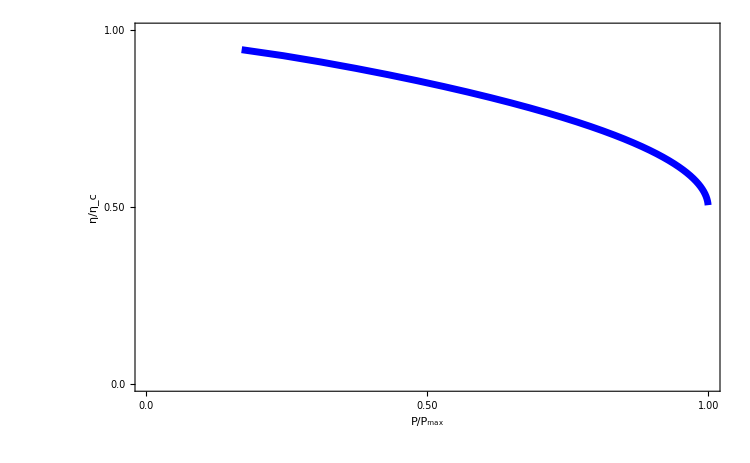

```mathematica
data2=Import["check20.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data2},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

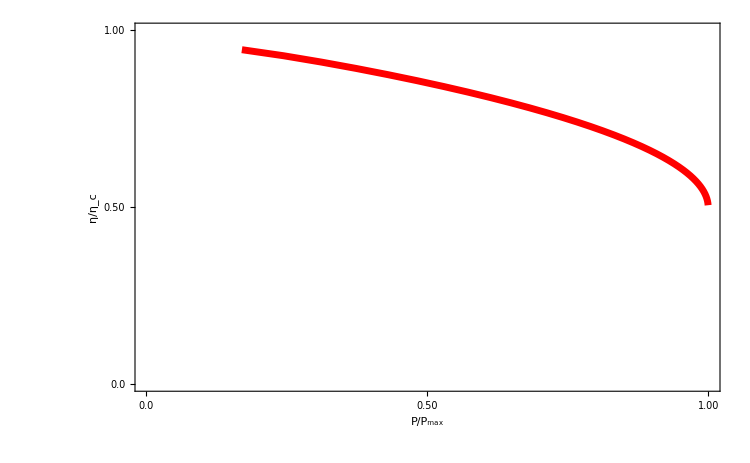

```mathematica
data2=Import["check40.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data2},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750]
```

# Non-linear chiral (E_1'=k_B θ+eV_g,E_2'=k_B θ+eV_g)(Voltage-temperature probe)

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=3.7;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=(2ec)/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=2/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,T3,P/(2*0.316493),2*η}];
},{Vg,-1,20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check122.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.05252×10^-20 and 2.19433×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.05252×10^-20 and 2.19433×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.76747×10^-13 and 1.97659×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.34224×10^-17 and 7.80795×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.51956×10^-16 and 1.94517×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.50389×10^-16 and 5.79789×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.7036×10^-17 and 7.23721×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.1672×10^-16 and 2.68432×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.65382×10^-16 and 7.21809×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.90908×10^-17 and 3.63336×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.27364×10^-16 and 1.65443×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.26674×10^-17 and 7.50736×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.08544×10^-17 and 2.16605×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.19646×10^-16 and 1.21941×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.2602×10^-13 and 1.29256×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.57527×10^-19 and 1.13071×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.35663×10^-18 and 5.92694×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.75428×10^-17 and 7.02383×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.51328×10^-18 and 3.10565×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.83411×10^-17 and 2.15215×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.5918×10^-18 and 3.02192×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.32549×10^-18 and 1.54627×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.4663×10^-17 and 1.12637×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2294×10^-18 and 1.52289×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03255×10^-17 and 5.36767×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.1164×10^-17 and 3.46561×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.57485×10^-18 and 7.69184×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.72908×10^-19 and 3.11143×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.61647×10^-18 and 2.44866×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.1122×10^-19 and 3.16429×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.88176×10^-14 and 2.3185×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.57179×10^-13 and 1.95234×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.54511×10^-19 and 1.49468×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03346×10^-14 and 7.42324×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.63104×10^-14 and 5.62076×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.37514×10^-14 and 3.78627×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.13531×10^-15 and 2.45091×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.87123×10^-15 and 2.23939×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.75278×10^-15 and 2.92807×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.77542×10^-16 and 1.26133×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2586×10^-15 and 1.18274×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.78534×10^-15 and 1.17226×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{1177.95,Null}

```mathematica
"check122.dat"
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

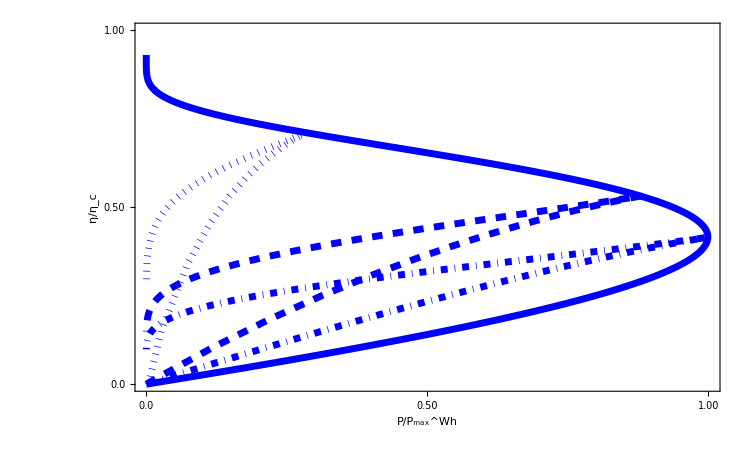

```mathematica
data1=Import["check120.dat"][[All,{4,5}]];
data2=Import["check121.dat"][[All,{4,5}]];
data3=Import["check122.dat"][[All,{4,5}]];
data4=Import["check12.dat"][[All,{4,5}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue,DotDashed],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[7.5]],Directive[AbsoluteThickness[5],Opacity[1],Blue,Dotted],Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

# Non-linear helical (E_1'=k_B θ+eV_g,E_2'=k_B θ+eV_g)(Voltage-temperature probe)

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=3.7;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=ec/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,T3,P/(2*0.316493),2*η}];
},{Vg,-1,20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check142.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.91935×10^-13 and 2.62259×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.3633×10^-13 and 1.74909×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.03491×10^-13 and 7.74262×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.92202×10^-13 and 5.68935×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.29213×10^-13 and 2.45133×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.64426×10^-13 and 1.63287×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.26565×10^-14 and 1.2444×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.44128×10^-13 and 3.71532×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.54117×10^-15 and 1.25091×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.96268×10^-15 and 7.06562×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.32707×10^-14 and 2.66406×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.71924×10^-15 and 7.59724×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.62381×10^-16 and 4.41608×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.54366×10^-15 and 1.97464×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.79551×10^-16 and 4.0831×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.80292×10^-16 and 1.74191×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.31735×10^-15 and 8.46066×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.8708×10^-16 and 1.50196×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.93732×10^-17 and 3.88504×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.37992×10^-16 and 2.56305×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.1525×10^-17 and 4.03478×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.13312×10^-17 and 3.61128×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.02859×10^-16 and 2.46254×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.78363×10^-17 and 3.22806×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.2313×10^-18 and 1.51581×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.19101×10^-17 and 1.1649×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.65171×10^-18 and 8.82976×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.07976×10^-19 and 8.40008×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.14508×10^-18 and 6.4644×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.57689×10^-18 and 7.28676×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.72722×10^-15 and 1.54219×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.26144×10^-14 and 1.33733×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.82277×10^-14 and 6.19262×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.31678×10^-18 and 3.37×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.24366×10^-17 and 2.84504×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.89183×10^-19 and 1.19694×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.61833×10^-15 and 7.23383×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.14865×10^-15 and 5.37917×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.25567×10^-15 and 5.68755×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.08863×10^-16 and 1.20465×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.72758×10^-16 and 1.17584×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.7355×10^-16 and 2.89972×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.06156×10^-17 and 1.31899×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.91949×10^-17 and 1.1672×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.16112×10^-17 and 1.19539×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{1385.17,Null}

check14.dat

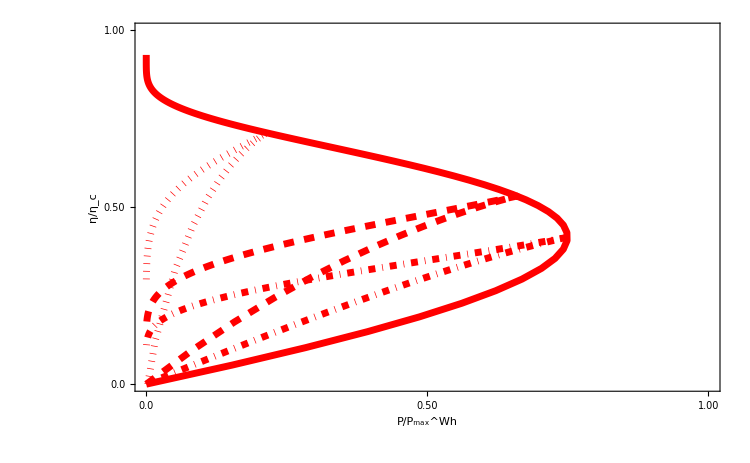

```mathematica
data1=Import["check140.dat"][[All,{4,5}]];
data2=Import["check141.dat"][[All,{4,5}]];
data3=Import["check142.dat"][[All,{4,5}]];
data4=Import["check143.dat"][[All,{4,5}]];
Needs["PlotLegends`"]
A3=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red,DotDashed],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[7.5]],Directive[AbsoluteThickness[5],Opacity[1],Red,Dotted],Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,35],LabelStyle->Directive[Bold,Black,35]]
```

# Linear chiral refrigerator (E_1'=k_B θ+eV_g,E_2'=k_B θ+eV_g)(Voltage-temperature probe)

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T12uu=TX TY;
T13uu=TX (1-TY);
T21uu=0;
T22uu=(1-TY);
T23uu=TY;
T31uu=TX;
T32uu=TY(1-TX);
T33uu=(1-TX)( 1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=x1*a/ec;
V=0.84*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(1-T11uu)*G0*df,{G,n0,n1}];
G12=NIntegrate[(-T12uu)*G0*df,{G,n0,n1}];
G13=NIntegrate[(-T13uu)*G0*df,{G,n0,n1}];
G31=NIntegrate[(-T31uu)*G0*df,{G,n0,n1}];
G32=NIntegrate[(-T32uu)*G0*df,{G,n0,n1}];
G33=NIntegrate[(1-T33uu)*G0*df,{G,n0,n1}];
L11=NIntegrate[(1-T11uu)*(G-μ)*L0*df,{G,n0,n1}];
L12=NIntegrate[(-T12uu)*(G-μ)*L0*df,{G,n0,n1}];
L13=NIntegrate[(-T13uu)*(G-μ)*L0*df,{G,n0,n1}];
L23=NIntegrate[(-T23uu)*(G-μ)*L0*df,{G,n0,n1}];
L33=NIntegrate[(1-T33uu)*(G-μ)*L0*df,{G,n0,n1}];
L31=NIntegrate[(-T31uu)*(G-μ)*L0*df,{G,n0,n1}];
L32=NIntegrate[(-T32uu)*(G-μ)*L0*df,{G,n0,n1}];
π11=NIntegrate[(1-T11uu)*(G-μ)*Lp*df,{G,n0,n1}];
π12=NIntegrate[(-T12uu)*(G-μ)*Lp*df,{G,n0,n1}];
π13=NIntegrate[(-T13uu)*(G-μ)*Lp*df,{G,n0,n1}];
π31=NIntegrate[(-T31uu)*(G-μ)*Lp*df,{G,n0,n1}];
π33=NIntegrate[(1-T33uu)*(G-μ)*Lp*df,{G,n0,n1}];
K11=NIntegrate[(1-T11uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K12=NIntegrate[(-T12uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K13=NIntegrate[(-T13uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K31=NIntegrate[(-T31uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K32=NIntegrate[(-T32uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K33=NIntegrate[(1-T33uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
ηr1=J1/P1*0.01;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z,-J1/Jq,ηr1}];
},{x1,4,84,2}];//AbsoluteTiming
list=Sort[list1];
Export["check30.dat",list]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.89546}. NIntegrate obtained 0.0000454177 and 7.86841×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {15.8089}. NIntegrate obtained 1.12577×10^-7 and 8.7826×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {27.8667}. NIntegrate obtained 6.91729×10^-13 and 2.03864×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {39.9373}. NIntegrate obtained 4.2501×10^-18 and 2.09806×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained -0.000281215 and 8.27778×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.89546}. NIntegrate obtained -0.0000446958 and 6.46594×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {15.8089}. NIntegrate obtained -1.10763×10^-7 and 6.5107×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {21.975}. NIntegrate obtained 2.79063×10^-10 and 5.11612×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {28.0101}. NIntegrate obtained -6.8072×10^-13 and 1.07039×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {33.8278}. NIntegrate obtained 1.71462×10^-15 and 1.12281×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {39.9373}. NIntegrate obtained -4.18195×10^-18 and 2.59982×10^-20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {45.7835}. NIntegrate obtained 1.05298×10^-20 and 1.21848×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained -0.000281215 and 8.27778×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.89546}. NIntegrate obtained -7.21908×10^-7 and 7.22644×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {15.8089}. NIntegrate obtained -1.12577×10^-7 and 8.7826×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained -0.00112464 and 3.27638×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {21.973}. NIntegrate obtained -2.74622×10^-10 and 2.40451×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {27.8667}. NIntegrate obtained -6.91729×10^-13 and 2.03864×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {33.8278}. NIntegrate obtained -1.68733×10^-15 and 1.90965×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {39.9373}. NIntegrate obtained -4.2501×10^-18 and 2.09806×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {45.7835}. NIntegrate obtained -1.03728×10^-20 and 1.60291×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {21.9776}. NIntegrate obtained -4.48542×10^-12 and 1.79214×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.00006}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {33.8278}. NIntegrate obtained -1.71462×10^-15 and 1.12281×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {61.31}. NIntegrate obtained 1.18555×10^-27 and 2.4992×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {51.9892}. NIntegrate obtained 2.61129×10^-23 and 5.76732×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {57.4771}. NIntegrate obtained 6.48026×10^-26 and 5.89128×10^-28 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {61.9944}. NIntegrate obtained -1.16532×10^-27 and 2.39624×10^-30 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {65.6344}. NIntegrate obtained 2.19096×10^-29 and 5.3617×10^-31 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {51.9892}. NIntegrate obtained -2.56969×10^-23 and 1.26109×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {57.4771}. NIntegrate obtained -6.3705×10^-26 and 1.46072×10^-28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {69.6771}. NIntegrate obtained 3.92266×10^-31 and 1.36053×10^-32 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {61.31}. NIntegrate obtained -1.18555×10^-27 and 2.4992×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.00006}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {65.6344}. NIntegrate obtained -2.14084×10^-29 and 4.48862×10^-32 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {69.6771}. NIntegrate obtained -3.84347×10^-31 and 2.13258×10^-32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {73.2429}. NIntegrate obtained 7.2246×10^-33 and 2.93036×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {77.1438}. NIntegrate obtained 1.34084×10^-34 and 6.69155×10^-36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {81.4236}. NIntegrate obtained 2.38328×10^-36 and 1.09006×10^-37 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {57.4771}. NIntegrate obtained -6.48026×10^-26 and 5.89128×10^-28 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {73.2429}. NIntegrate obtained -7.15685×10^-33 and 3.3407×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {77.1438}. NIntegrate obtained -1.33024×10^-34 and 6.01203×10^-36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {81.4236}. NIntegrate obtained -2.31739×10^-36 and 2.71492×10^-37 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {65.6344}. NIntegrate obtained -2.19096×10^-29 and 5.3617×10^-31 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {69.6771}. NIntegrate obtained -3.92266×10^-31 and 1.36053×10^-32 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {73.2429}. NIntegrate obtained -7.2246×10^-33 and 2.93036×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {77.1438}. NIntegrate obtained -1.34084×10^-34 and 6.69155×10^-36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {81.4236}. NIntegrate obtained -2.38328×10^-36 and 1.09006×10^-37 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{12.9441,Null}

check30.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

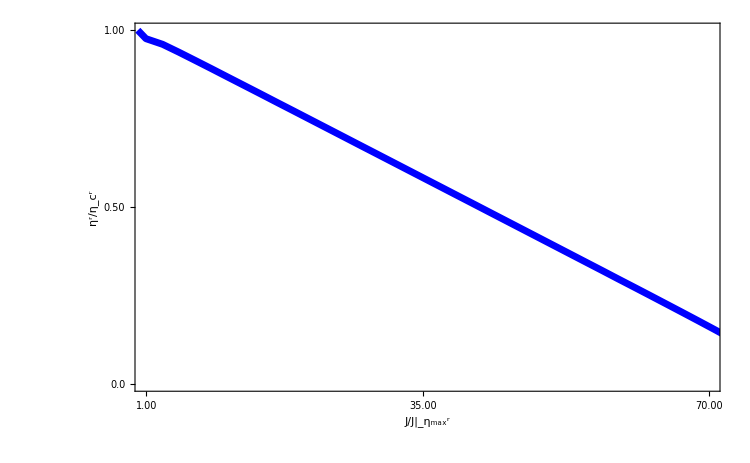

```mathematica
data2=Import["check30.dat"][[All,{10,11}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data2},Frame->True,PlotRange->{{1.0,70},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.000,"1.00"},{70,"70.00"},{35,"35.00"}},None}},FrameLabel->{Style["J/J|_(η_max^r)",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750]
```

# Linear helical refrigerator (E_1'=k_B θ+eV_g,E_2'=k_B θ+eV_g) (voltage-temperature probe)

```mathematica
kb=1;
T=1;
θ=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
V=0.84*a/ec;
Vg=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=2+ec*Vg;
E1=1+ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
ηr1=J1/P1*0.01;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,Jq*h/(kb^2*θ*δT),Subscript[η, r],-J1*h/(kb^2*θ*δT)/(2.15*10^-7),-J1/Jq,ηr1}]
},{x1,4,84,4}];//AbsoluteTiming
list=Sort[list1];
Export["check40.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 100 recursive bisections in G near {G} = {1.}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{8.30609,Null}

check40.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

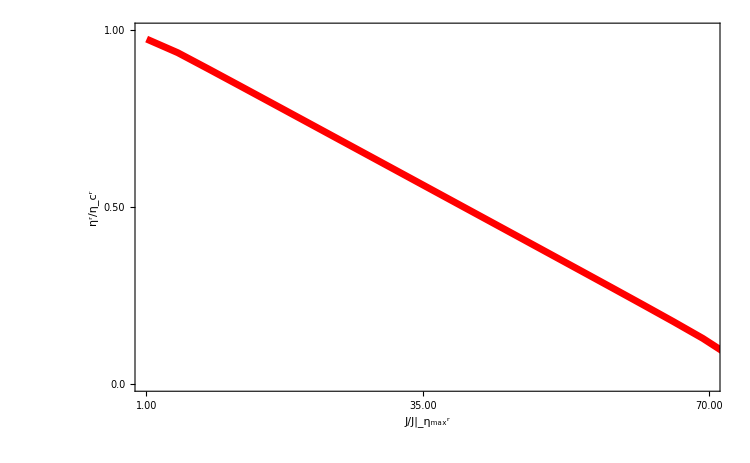

```mathematica
data2=Import["check40.dat"][[All,{5,6}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data2},Frame->True,PlotRange->{{1.0,70},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.000,"1.00"},{70,"70.00"},{35,"35.00"}},None}},FrameLabel->{Style["J/J|_(η_max^r)",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750]
```

# Nonlinear chiral refrigerator (E_1'=k_B θ+eV_g,E_2'=k_B θ+eV_g)(voltage-temperature probe)

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=20;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,V},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=(2*ec)/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=2/h NIntegrate[(G)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
ηr=J1/P;
list=AppendTo[list1,{Vg,P/(2*0.316493),-J1/(2*0.82),ηr}];
},{Vg,0.0,17.2,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check60.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.96841×10^-14 and 3.73366×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.90882×10^-13 and 1.56255×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.77914×10^-14 and 7.02607×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.04409×10^-13 and 2.07297×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.54581×10^-13 and 6.47351×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.58309×10^-13 and 1.30291×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.22208×10^-13 and 1.03812×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.57843×10^-12 and 1.92625×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.69709×10^-14 and 7.95108×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.44811×10^-14 and 9.09571×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.23502×10^-13 and 6.37393×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.29586×10^-13 and 2.37878×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.67268×10^-13 and 1.035×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.92335×10^-14 and 4.37922×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.93397×10^-12 and 2.95583×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.50699×10^-13 and 1.13708×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.33725×10^-14 and 9.75206×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.62951×10^-13 and 1.79143×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.46841×10^-12 and 1.68327×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.78112×10^-13 and 3.69616×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.61371×10^-15 and 3.60861×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.7217×10^-16 and 2.13317×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.14233×10^-14 and 2.21166×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.19031×10^-15 and 1.45692×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.56524×10^-15 and 1.67484×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.0541×10^-17 and 6.24761×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.63457×10^-14 and 2.98813×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.84258×10^-16 and 1.5589×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.43907×10^-15 and 1.20628×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.955×10^-14 and 6.52034×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.71009×10^-15 and 1.86766×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.71009×10^-15 and 1.86766×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.37016×10^-19 and 3.57094×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.42686×10^-20 and 1.8898×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.08682×10^-15 and 1.54319×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2298×10^-18 and 1.16169×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.73875×10^-19 and 3.57554×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.97654×10^-14 and 3.15118×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{94.6872,Null}

check60.dat

# Nonlinear helical refrigerator (E_1'=k_B θ+eV_g,E_2'=k_B θ+eV_g)(voltage-temperature probe)

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=20;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GaussKronrodRule",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}}];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=1/h NIntegrate[(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G)(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=J1/(V*I1);
list=AppendTo[list1,{Vg,V3,J1/(2*0.82),η}];
},{Vg,0,17.2,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check80.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.97988×10^-17 and 6.50032×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.21183×10^-12 and 3.31937×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.01134×10^-15 and 1.71931×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.11035×10^-15 and 1.23376×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.37199×10^-16 and 5.74226×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.58541×10^-13 and 2.98729×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.68269×10^-15 and 1.46999×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.77775×10^-15 and 1.41924×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.65677×10^-17 and 1.49369×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.2097×10^-12 and 1.08596×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.39982×10^-13 and 6.55555×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.91843×10^-14 and 5.48231×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.99817×10^-16 and 2.99006×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.73574×10^-14 and 9.73996×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.22672×10^-15 and 2.28479×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.58541×10^-13 and 2.98729×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.21183×10^-12 and 3.31937×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.01134×10^-15 and 1.71931×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.11035×10^-15 and 1.23376×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.37199×10^-16 and 5.74226×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.28356×10^-18 and 2.87666×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.68269×10^-15 and 1.46999×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.77775×10^-15 and 1.41924×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.60615×10^-16 and 8.71368×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.65166×10^-16 and 1.2949×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.89248×10^-18 and 5.0868×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.16956×10^-15 and 3.20887×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.0326×10^-15 and 9.49462×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.52203×10^-17 and 4.08179×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.01432×10^-14 and 2.70481×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.76129×10^-14 and 4.11097×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.85252×10^-19 and 1.57218×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.13067×10^-18 and 2.34125×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.22508×10^-19 and 2.11357×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.67496×10^-18 and 7.49716×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.65166×10^-16 and 1.2949×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.05723×10^-18 and 5.13113×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.76129×10^-14 and 4.11097×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.27264×10^-18 and 1.43492×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.13067×10^-18 and 2.34125×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.16956×10^-15 and 3.20887×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.43148×10^-19 and 2.2046×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.67496×10^-18 and 7.49716×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.12989×10^-19 and 4.35442×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.85252×10^-19 and 1.57218×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.37284×10^-19 and 8.00354×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.21238×10^-18 and 1.02495×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{26.4621,Null}

check80.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

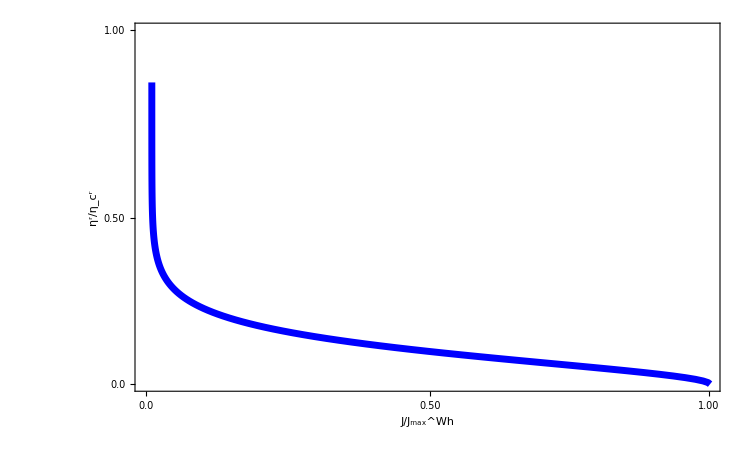

```mathematica
data2=Import["check60.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data2},Frame->True,PlotRange->{{-0.01,1},{0.06,1}},Frame->True,FrameTicks->{{{{0.06,"0.0"},{1,"1.00"},{0.50,"0.50"}},None},{{{-0.01,"0.0"},{1,"1.00"},{0.50,"0.50"}},None}},FrameLabel->{Style["J/J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

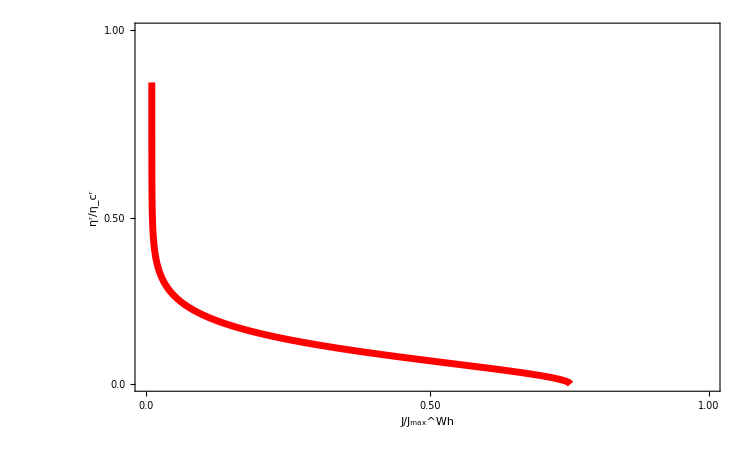

```mathematica
data2=Import["check80.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data2},Frame->True,PlotRange->{{-0.01,1},{0.06,1}},Frame->True,FrameTicks->{{{{0.06,"0.0"},{1,"1.00"},{0.50,"0.50"}},None},{{{-0.01,"0.0"},{1,"1.00"},{0.50,"0.50"}},None}},FrameLabel->{Style["J/J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
Export["/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig3supple.pdf",A5,"PDF"]
```

/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig3supple.pdf

```mathematica
Export["/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig4supple.pdf",A5,"PDF"]
```

/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig4supple.pdf

```mathematica
Export["/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig.4(a).pdf",A1,ImageResolution->300]
```

/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig.4(a).pdf

```mathematica
Export["/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig4.pdf",A5,"PDF"]
```

/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig4.pdf

```mathematica
Export["/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig.4(c).pdf",A3,ImageResolution->300]
```

/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig.4(c).pdf

```mathematica
Export["/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig.4(d).pdf",A4,ImageResolution->300]
```

/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig.4(d).pdf

```mathematica
Export["/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig5.pdf",A5,"PDF"]
```

/home/sachiraj/Phd_Work/Second work(Thermoelectricity)/fig5.pdf

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T12uu=TX TY;
T13uu=TX (1-TY);
T21uu=0;
T22uu=(1-TY);
T23uu=TY;
T31uu=TX;
T32uu=TY(1-TX);
T33uu=(1-TX)( 1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(1-T11uu)*G0*df,{G,n0,n1}];
G12=NIntegrate[(-T12uu)*G0*df,{G,n0,n1}];
G13=NIntegrate[(-T13uu)*G0*df,{G,n0,n1}];
G31=NIntegrate[(-T31uu)*G0*df,{G,n0,n1}];
G32=NIntegrate[(-T32uu)*G0*df,{G,n0,n1}];
G33=NIntegrate[(1-T33uu)*G0*df,{G,n0,n1}];
L11=NIntegrate[(1-T11uu)*(G-μ)*L0*df,{G,n0,n1}];
L12=NIntegrate[(-T12uu)*(G-μ)*L0*df,{G,n0,n1}];
L13=NIntegrate[(-T13uu)*(G-μ)*L0*df,{G,n0,n1}];
L23=NIntegrate[(-T23uu)*(G-μ)*L0*df,{G,n0,n1}];
L33=NIntegrate[(1-T33uu)*(G-μ)*L0*df,{G,n0,n1}];
L31=NIntegrate[(-T31uu)*(G-μ)*L0*df,{G,n0,n1}];
L32=NIntegrate[(-T32uu)*(G-μ)*L0*df,{G,n0,n1}];
π11=NIntegrate[(1-T11uu)*(G-μ)*Lp*df,{G,n0,n1}];
π12=NIntegrate[(-T12uu)*(G-μ)*Lp*df,{G,n0,n1}];
π13=NIntegrate[(-T13uu)*(G-μ)*Lp*df,{G,n0,n1}];
π31=NIntegrate[(-T31uu)*(G-μ)*Lp*df,{G,n0,n1}];
π33=NIntegrate[(1-T33uu)*(G-μ)*Lp*df,{G,n0,n1}];
K11=NIntegrate[(1-T11uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K12=NIntegrate[(-T12uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K13=NIntegrate[(-T13uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K31=NIntegrate[(-T31uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K32=NIntegrate[(-T32uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K33=NIntegrate[(1-T33uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
list=AppendTo[list1,{x1,T*Sc/Pc}];
},{x1,0,80,1}];//AbsoluteTiming
list=Sort[list1];
Export["check200.dat",list]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.9092}. NIntegrate obtained 0.0000167091 and 2.35535×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.9092}. NIntegrate obtained -0.0000164417 and 4.06804×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.9092}. NIntegrate obtained -2.6744×10^-7 and 6.26319×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {0.406624}. NIntegrate obtained 1.26213×10^-19 and 4.41453×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {0.406624}. NIntegrate obtained 1.26213×10^-19 and 4.41453×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {0.406624}. NIntegrate obtained 1.26213×10^-19 and 4.41453×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.735}. NIntegrate obtained 7.62067×10^-10 and 2.04458×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.951}. NIntegrate obtained -7.46499×10^-10 and 7.64737×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {20.735}. NIntegrate obtained -1.05974×10^-11 and 7.42024×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {30.8935}. NIntegrate obtained 3.44392×10^-14 and 1.66793×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {30.8935}. NIntegrate obtained -3.38911×10^-14 and 2.26549×10^-18 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {30.8935}. NIntegrate obtained -3.44392×10^-14 and 1.66793×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {40.8602}. NIntegrate obtained 1.56379×10^-18 and 8.9162×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {40.8602}. NIntegrate obtained -1.53926×10^-18 and 4.1024×10^-21 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {40.8602}. NIntegrate obtained -1.56379×10^-18 and 8.9162×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {50.5294}. NIntegrate obtained 7.09848×10^-23 and 4.45247×10^-26 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {50.5294}. NIntegrate obtained -6.9853×10^-23 and 1.16436×10^-25 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.00006}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {60.6392}. NIntegrate obtained 3.20283×10^-27 and 1.09522×10^-28 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {60.6392}. NIntegrate obtained -3.16484×10^-27 and 1.36423×10^-28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {70.5393}. NIntegrate obtained 1.4393×10^-31 and 6.28127×10^-33 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {70.5393}. NIntegrate obtained -1.41686×10^-31 and 8.45717×10^-33 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {70.5393}. NIntegrate obtained -1.4393×10^-31 and 6.28127×10^-33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {60.6392}. NIntegrate obtained -3.20283×10^-27 and 1.09522×10^-28 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{28.1904,Null}

check200.dat

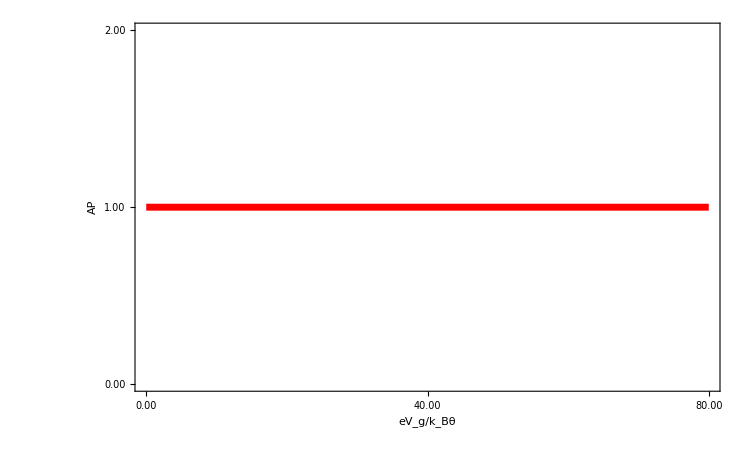

```mathematica
data4=Import["check200.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
A4=ListLinePlot[{data4},Frame->True,PlotRange->{{0,80},{0.0,2.00}},Frame->True,FrameTicks->{{{{0.00,"0.00"},{1.0,"1.00"},{2.0,"2.00"}},None},{{{0,"0.00"},{40,"40.00"},{80,"80.00"}},None}},FrameLabel->{Style["eV_g/k_Bθ",45,Bold,Black],Style["AP",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
Export["/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig3supple.pdf",A4,ImageResolution->300]
```

/home/sachiraj/Phd_Work/Chiral thermoelectrics/fig3supple.pdf

# Linear Chiral (E_1'=k_B θ+eV_g,E_2'=2 k_B θ+eV_g)(Voltage temperature probe)

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T12uu=TX TY;
T13uu=TX (1-TY);
T21uu=0;
T22uu=(1-TY);
T23uu=TY;
T31uu=TX;
T32uu=TY(1-TX);
T33uu=(1-TX)( 1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=83.8*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=2+ec*Vg;
E1=1+ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(1-T11uu)*G0*df,{G,n0,n1}];
G12=NIntegrate[(-T12uu)*G0*df,{G,n0,n1}];
G13=NIntegrate[(-T13uu)*G0*df,{G,n0,n1}];
G31=NIntegrate[(-T31uu)*G0*df,{G,n0,n1}];
G32=NIntegrate[(-T32uu)*G0*df,{G,n0,n1}];
G33=NIntegrate[(1-T33uu)*G0*df,{G,n0,n1}];
L11=NIntegrate[(1-T11uu)*(G-μ)*L0*df,{G,n0,n1}];
L12=NIntegrate[(-T12uu)*(G-μ)*L0*df,{G,n0,n1}];
L13=NIntegrate[(-T13uu)*(G-μ)*L0*df,{G,n0,n1}];
L23=NIntegrate[(-T23uu)*(G-μ)*L0*df,{G,n0,n1}];
L33=NIntegrate[(1-T33uu)*(G-μ)*L0*df,{G,n0,n1}];
L31=NIntegrate[(-T31uu)*(G-μ)*L0*df,{G,n0,n1}];
L32=NIntegrate[(-T32uu)*(G-μ)*L0*df,{G,n0,n1}];
π11=NIntegrate[(1-T11uu)*(G-μ)*Lp*df,{G,n0,n1}];
π12=NIntegrate[(-T12uu)*(G-μ)*Lp*df,{G,n0,n1}];
π13=NIntegrate[(-T13uu)*(G-μ)*Lp*df,{G,n0,n1}];
π31=NIntegrate[(-T31uu)*(G-μ)*Lp*df,{G,n0,n1}];
π33=NIntegrate[(1-T33uu)*(G-μ)*Lp*df,{G,n0,n1}];
K11=NIntegrate[(1-T11uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K12=NIntegrate[(-T12uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K13=NIntegrate[(-T13uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K31=NIntegrate[(-T31uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K32=NIntegrate[(-T32uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K33=NIntegrate[(1-T33uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z}];
},{x1,0,0.84,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check100.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{17.5101,Null}

check100.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

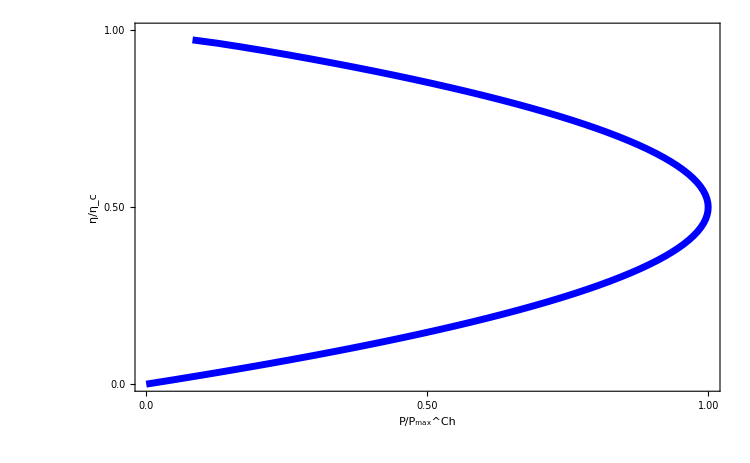

```mathematica
data2=Import["check100.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data2},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max^Ch",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750]
```

# Linear helical (E_1'=k_B θ+eV_g,E_2'=2 k_B θ+eV_g)(Voltage temperature probe)

```mathematica
kb=1;
T=1;
θ=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=83.8*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=2+ec*Vg;
E1=1+ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z,Jq*h/(kb^2*θ*δT),Subscript[η, r]}]
},{x1,0,0.84,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check101.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{13.9512,Null}

check101.dat

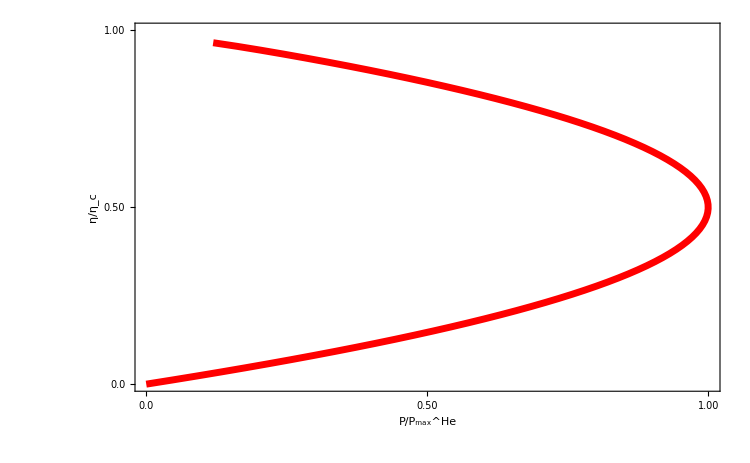

```mathematica
data4=Import["check101.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data4},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max^He",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750]
```

# Linear chiral refrigerator (E_1'=k_B θ+eV_g,E_2'=2 k_B θ+eV_g)(Voltage-temperature probe)

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T12uu=TX TY;
T13uu=TX (1-TY);
T21uu=0;
T22uu=(1-TY);
T23uu=TY;
T31uu=TX;
T32uu=TY(1-TX);
T33uu=(1-TX)( 1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=83.8*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=2+ec*Vg;
E1=1+ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(1-T11uu)*G0*df,{G,n0,n1}];
G12=NIntegrate[(-T12uu)*G0*df,{G,n0,n1}];
G13=NIntegrate[(-T13uu)*G0*df,{G,n0,n1}];
G31=NIntegrate[(-T31uu)*G0*df,{G,n0,n1}];
G32=NIntegrate[(-T32uu)*G0*df,{G,n0,n1}];
G33=NIntegrate[(1-T33uu)*G0*df,{G,n0,n1}];
L11=NIntegrate[(1-T11uu)*(G-μ)*L0*df,{G,n0,n1}];
L12=NIntegrate[(-T12uu)*(G-μ)*L0*df,{G,n0,n1}];
L13=NIntegrate[(-T13uu)*(G-μ)*L0*df,{G,n0,n1}];
L23=NIntegrate[(-T23uu)*(G-μ)*L0*df,{G,n0,n1}];
L33=NIntegrate[(1-T33uu)*(G-μ)*L0*df,{G,n0,n1}];
L31=NIntegrate[(-T31uu)*(G-μ)*L0*df,{G,n0,n1}];
L32=NIntegrate[(-T32uu)*(G-μ)*L0*df,{G,n0,n1}];
π11=NIntegrate[(1-T11uu)*(G-μ)*Lp*df,{G,n0,n1}];
π12=NIntegrate[(-T12uu)*(G-μ)*Lp*df,{G,n0,n1}];
π13=NIntegrate[(-T13uu)*(G-μ)*Lp*df,{G,n0,n1}];
π31=NIntegrate[(-T31uu)*(G-μ)*Lp*df,{G,n0,n1}];
π33=NIntegrate[(1-T33uu)*(G-μ)*Lp*df,{G,n0,n1}];
K11=NIntegrate[(1-T11uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K12=NIntegrate[(-T12uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K13=NIntegrate[(-T13uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K31=NIntegrate[(-T31uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K32=NIntegrate[(-T32uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K33=NIntegrate[(1-T33uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
ηr1=J1/P1*0.01;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z,-J1/Jq,ηr1}];
},{x1,0.84,8,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check50.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -1.47776×10^-37 and 5.42722×10^-39 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{71.656,Null}

check50.dat

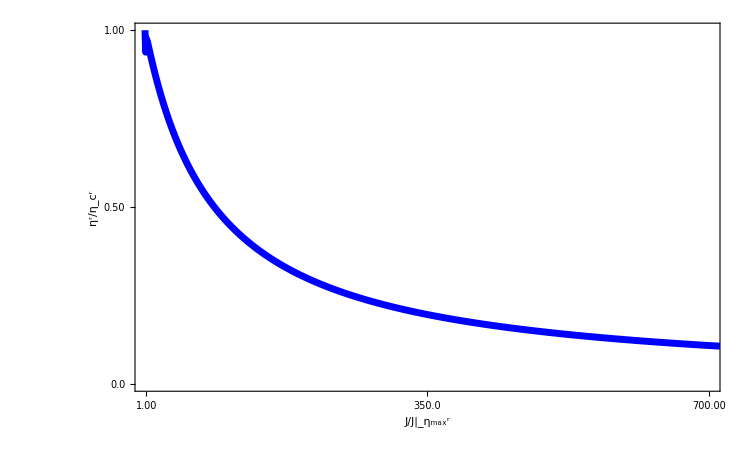

```mathematica
data2=Import["check50.dat"][[All,{10,11}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data2},Frame->True,PlotRange->{{1.00001,700},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0001,"1.00"},{350,"350.0"},{700,"700.00"}},None}},FrameLabel->{Style["J/J|_(η_max^r)",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750]
```

# Linear helical refrigerator (E_1'=k_B θ+eV_g,E_2'=2 k_B θ+eV_g)(Voltage-temperature probe)

```mathematica
kb=1;
T=1;
θ=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=83.80*a/ec;
V=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=2+ec*Vg;
E1=1+ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
ηr1=J1/P1*0.01;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,Jq*h/(kb^2*θ*δT),Subscript[η, r],-J1*h/(kb^2*θ*δT)/(2.15*10^-7),-J1/Jq,ηr1}]
},{x1,0.84,8,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check40.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 2.95553×10^-37 and 1.08544×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {84.9124}. NIntegrate obtained -5.60405×10^-38 and 3.85913×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -2.39512×10^-37 and 1.47035×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{49.2289,Null}

check40.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

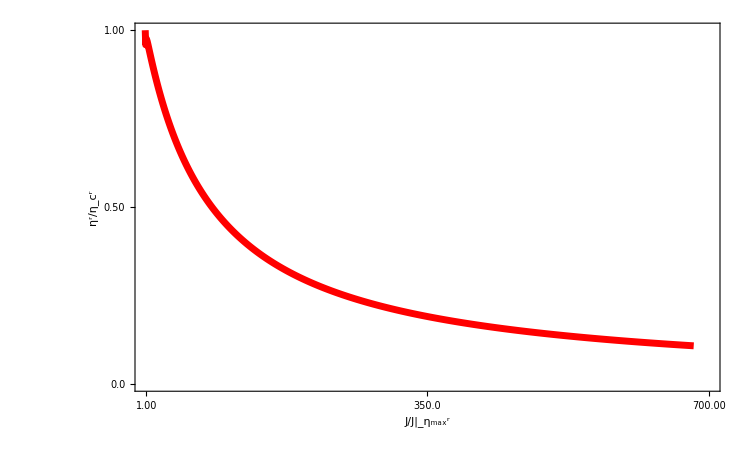

```mathematica
data2=Import["check40.dat"][[All,{5,6}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data2},Frame->True,PlotRange->{{1.00001,700},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.0001,"1.00"},{350,"350.0"},{700,"700.00"}},None}},FrameLabel->{Style["J/J|_(η_max^r)",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750]
```

# Non-linear chiral (E_1'=k_B θ+eV_g,E_2'=2 k_B θ+eV_g)(Voltage-temperature probe)

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=3.7;
Vg=1.7;
E1=Vg;
E2=Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=(2ec)/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=2/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=(V*I1)/(2*0.316493)
η=(P/J1)*2
```

-0.424443

3.98401

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=Vg;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=Vg;
E2=Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=(2ec)/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=2/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V,V3,T3,P/(2*0.316493),2*η}];
},{Vg,-5,15,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check53.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.65083×10^-13 and 2.41606×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.47905×10^-15 and 1.48745×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.88899×10^-13 and 1.10822×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.64184×10^-11 and 5.92057×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.93659×10^-15 and 4.17374×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.54386×10^-11 and 8.10168×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.00817×10^-12 and 5.97169×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.08028×10^-14 and 4.36608×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.08593×10^-12 and 4.45793×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.45693×10^-11 and 9.42977×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.75633×10^-14 and 1.01946×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.55294×10^-14 and 1.07587×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.64661×10^-12 and 3.56086×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.1332×10^-12 and 5.84522×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.90191×10^-14 and 1.31362×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2571×10^-10 and 1.41532×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.99649×10^-15 and 2.43691×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.52444×10^-12 and 1.04457×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.47739×10^-13 and 7.81543×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.19647×10^-15 and 3.58939×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.92332×10^-15 and 1.1523×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.06192×10^-12 and 8.97531×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.40119×10^-11 and 1.89532×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.52634×10^-11 and 2.72397×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.32503×10^-13 and 4.17099×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.01387×10^-13 and 2.02917×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.01697×10^-15 and 2.01607×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.25274×10^-14 and 1.1539×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.00579×10^-16 and 1.12646×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.66646×10^-16 and 6.96685×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.11965×10^-12 and 3.56413×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.39261×10^-14 and 3.10805×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.74994×10^-16 and 1.66451×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.38826×10^-17 and 5.38144×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.98258×10^-16 and 3.77442×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.44242×10^-14 and 1.71917×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.28977×10^-17 and 9.39587×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.88536×10^-13 and 1.66553×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.17694×10^-18 and 2.07359×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.68063×10^-17 and 1.76969×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.99289×10^-17 and 1.23025×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.54497×10^-16 and 1.25179×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.12989×10^-17 and 2.36796×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.18007×10^-15 and 1.12918×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.01842×10^-18 and 1.09955×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.54923×10^-17 and 1.12231×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.59232×10^-19 and 1.70244×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.87382×10^-15 and 9.39408×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.04375×10^-17 and 1.8443×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.67878×10^-17 and 9.34904×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.70731×10^-18 and 1.3847×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.15856×10^-18 and 3.17718×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.99988×10^-14 and 8.83413×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.66894×10^-17 and 5.11486×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.60871×10^-18 and 1.25782×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.3065×10^-19 and 1.36919×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.50174×10^-18 and 1.61999×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.21004×10^-16 and 5.80171×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.20477×10^-18 and 2.06421×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.27566×10^-18 and 1.13104×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.14378×10^-15 and 1.79649×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.07926×10^-17 and 1.94975×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.08279×10^-18 and 6.51856×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{52.46,Null}

check53.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

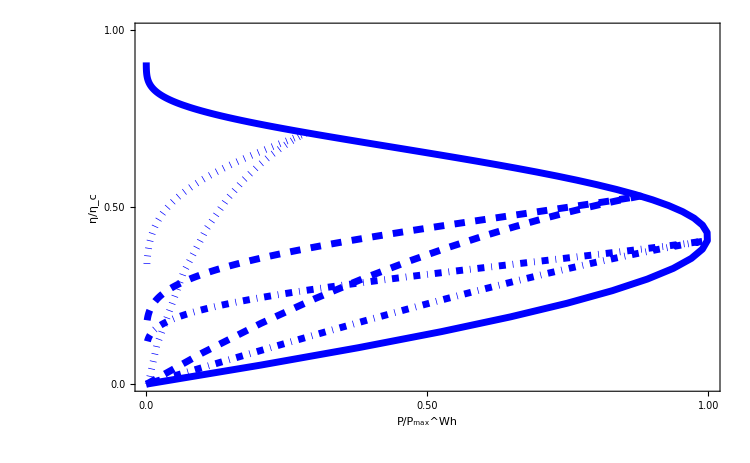

```mathematica
data1=Import["check50.dat"][[All,{5,6}]];
data2=Import["check51.dat"][[All,{5,6}]];
data3=Import["check52.dat"][[All,{5,6}]];
data4=Import["check53.dat"][[All,{5,6}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue,DotDashed],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[7.5]],Directive[AbsoluteThickness[5],Opacity[1],Blue,Dotted],Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

# Non-linear helical (E_1'=k_B θ+eV_g,E_2'=2 k_B θ+eV_g)(Voltage-temperature probe)

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=3.7;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=1+Vg;
E2=2+Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=ec/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,V3,T3,P/(2*0.316493),2*η}];
},{Vg,-5,20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check62.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.48219×10^-11 and 9.68198×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.81982×10^-15 and 2.00301×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.87038×10^-14 and 9.80756×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.39905×10^-12 and 1.84454×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.69266×10^-15 and 7.18879×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.5136×10^-11 and 9.03788×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.22211×10^-14 and 4.73051×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.73276×10^-13 and 3.62004×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.54091×10^-12 and 3.83094×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.36109×10^-15 and 1.90968×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.12814×10^-11 and 1.85024×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.51914×10^-12 and 1.94405×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.40735×10^-15 and 7.46149×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.53223×10^-14 and 2.04547×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.89129×10^-16 and 1.32956×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.61767×10^-13 and 8.9244×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.10852×10^-15 and 5.14778×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.04592×10^-15 and 3.75528×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.25269×10^-15 and 7.08448×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.12291×10^-15 and 2.53056×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.52488×10^-15 and 4.68358×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.21236×10^-15 and 1.00045×10^-17 for the integral and error estimates.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.56006×10^-10 and 2.76716×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

FindRoot::nlnum: The function value {2.89192×10^-13,NIntegrate[G (T31 (f3-f1)+T32 (f3-f2)),{G,-∞,∞},MaxRecursion→1000,AccuracyGoal→20,Method→GlobalAdaptive]} is not a list of numbers with dimensions {2} at {V3,T3} = {-2.03825,1.85151}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.21019×10^-15 and 2.19534×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.09944×10^-16 and 5.96604×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.38382×10^-13 and 4.3796×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.07672×10^-16 and 2.60288×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2555×10^-12 and 2.6516×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.70426×10^-17 and 3.02736×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.25029×10^-16 and 6.27236×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.09465×10^-16 and 1.9118×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.27029×10^-13 and 4.36061×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.40602×10^-14 and 2.44043×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.52884×10^-16 and 2.0357×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.91974×10^-13 and 8.12556×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.11943×10^-13 and 1.71698×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.10989×10^-15 and 1.64782×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.96837×10^-12 and 7.87039×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.39417×10^-16 and 3.08743×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.12984×10^-14 and 2.32843×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.74083×10^-17 and 6.25203×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.11409×10^-15 and 1.24067×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.4057×10^-14 and 7.68411×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.80608×10^-16 and 5.78262×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.73935×10^-17 and 5.24843×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.99508×10^-17 and 1.34352×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.88646×10^-16 and 1.02811×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.85183×10^-17 and 1.03566×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.23599×10^-14 and 4.11233×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.3615×10^-13 and 4.46997×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.20382×10^-14 and 3.56554×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.60117×10^-16 and 2.10974×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.72902×10^-14 and 1.03776×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.50828×10^-18 and 9.63921×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.95815×10^-15 and 1.98249×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.9867×10^-13 and 1.37267×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.85734×10^-17 and 1.38177×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.4803×10^-19 and 2.11775×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.0571×10^-17 and 2.8452×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.55879×10^-16 and 2.02996×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.91684×10^-14 and 1.4527×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.09079×10^-17 and 7.32799×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.33889×10^-17 and 2.50991×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.09981×10^-15 and 5.60803×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.12867×10^-14 and 8.20508×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.82086×10^-15 and 5.33303×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.53295×10^-17 and 3.81124×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.8628×10^-16 and 5.05936×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.04921×10^-18 and 3.58422×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.61864×10^-17 and 6.26404×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.17989×10^-17 and 2.73549×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.99988×10^-19 and 3.57629×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.02113×10^-15 and 2.24711×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.30643×10^-13 and 4.35062×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.02113×10^-15 and 2.24711×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.27556×10^-19 and 1.75711×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.81536×10^-18 and 2.87574×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.82014×10^-18 and 1.48471×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.39906×10^-16 and 1.19095×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.46239×10^-15 and 1.87655×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.62529×10^-14 and 1.5614×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.00655×10^-16 and 8.51886×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.80551×10^-16 and 1.18379×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.31199×10^-14 and 7.81344×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.20446×10^-16 and 1.02126×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.52223×10^-18 and 1.27871×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.27956×10^-14 and 1.2065×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.66511×10^-17 and 3.55941×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.08333×10^-18 and 1.20736×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.52987×10^-14 and 1.20571×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.44083×10^-18 and 4.45316×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.26955×10^-17 and 1.38726×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.38632×10^-16 and 3.76667×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.88386×10^-18 and 4.83043×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.33374×10^-17 and 3.87753×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.79445×10^-19 and 4.441×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{63.6004,Null}

check62.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

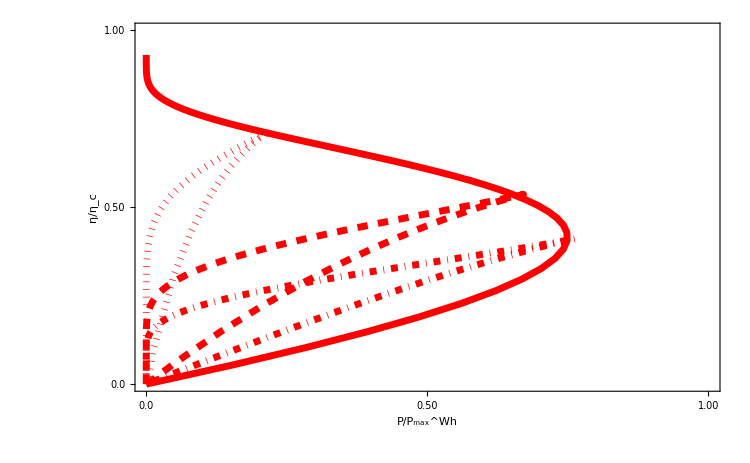

```mathematica
data1=Import["check60.dat"][[All,{4,5}]];
data2=Import["check61.dat"][[All,{4,5}]];
data3=Import["check62.dat"][[All,{4,5}]];
data4=Import["check63.dat"][[All,{4,5}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red,DotDashed],Directive[AbsoluteThickness[5],Opacity[1],Red,AbsoluteDashing[7.5]],Directive[AbsoluteThickness[5],Opacity[1],Red,Dotted],Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=20;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=1+Vg;
E2=2+Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,V},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=(2*ec)/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=2/h NIntegrate[(G)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
ηr=J1/P;
list=AppendTo[list1,{Vg,P/(2*0.316493),-J1/(2*0.82),ηr}];
},{Vg,-5.0,15.3,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check70.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.15985×10^-17 and 4.23064×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.26186×10^-15 and 3.24144×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.2424×10^-17 and 1.7386×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.68185×10^-16 and 1.95529×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.38265×10^-16 and 1.24185×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.49933×10^-15 and 6.3257×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.69914×10^-15 and 5.43791×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.75354×10^-17 and 1.68266×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.29727×10^-16 and 1.81168×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.14683×10^-16 and 2.01935×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.73927×10^-15 and 3.1855×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.70744×10^-18 and 1.3483×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.97327×10^-18 and 1.21973×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.192×10^-17 and 1.50754×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.68384×10^-17 and 1.15351×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.05567×10^-14 and 1.29116×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{50.3384,Null}

check70.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

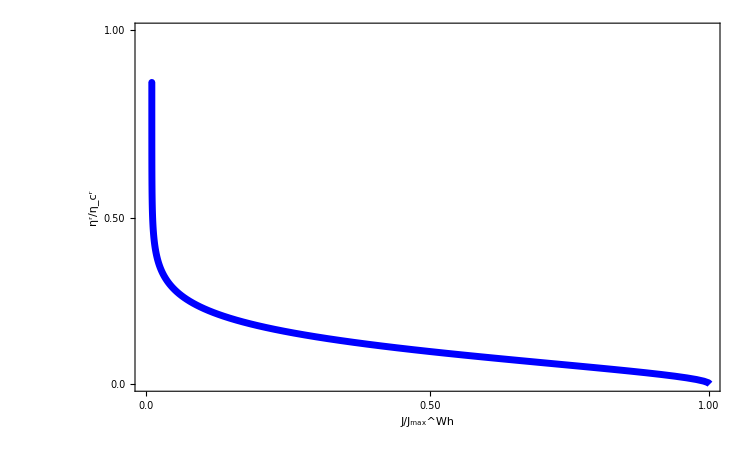

```mathematica
data2=Import["check70.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data2},Frame->True,PlotRange->{{-0.01,1},{0.06,1}},Frame->True,FrameTicks->{{{{0.06,"0.0"},{1,"1.00"},{0.50,"0.50"}},None},{{{-0.01,"0.0"},{1,"1.00"},{0.50,"0.50"}},None}},FrameLabel->{Style["J/J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=20;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=1+Vg;
E2=2+Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GaussKronrodRule",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}}];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=1/h NIntegrate[(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=1/h NIntegrate[(G)(T12(f2-f1)+T13(f3-f1)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=J1/(V*I1);
list=AppendTo[list1,{Vg,V3,J1/(2*0.82),η}];
},{Vg,-5,15.3,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check80.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.88984×10^-12 and 1.45132×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.12478×10^-14 and 7.75506×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.25318×10^-15 and 1.23518×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.65266×10^-16 and 1.62157×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.4409×10^-16 and 7.07801×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.04409×10^-16 and 3.23343×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.92988×10^-17 and 2.07875×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.50994×10^-14 and 3.89077×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.4548×10^-12 and 2.72549×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.67213×10^-12 and 2.46214×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.45678×10^-15 and 1.05739×10^-15 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.13642×10^-14 and 5.0926×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.46222×10^-15 and 1.01942×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.20382×10^-16 and 5.01107×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.39645×10^-16 and 4.28716×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.42972×10^-13 and 1.82281×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.88984×10^-12 and 1.45132×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.12478×10^-14 and 7.75506×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.25318×10^-15 and 1.23518×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.65266×10^-16 and 1.62157×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.4409×10^-16 and 7.07801×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.50994×10^-14 and 3.89077×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.86049×10^-16 and 4.3486×10^-17 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.82759×10^-18 and 2.1558×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.90947×10^-15 and 2.1156×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.27148×10^-14 and 1.11847×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.91541×10^-16 and 7.61226×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.90947×10^-15 and 2.1156×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.72239×10^-15 and 4.19139×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.70907×10^-17 and 3.29978×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.55538×10^-16 and 2.65371×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.91541×10^-16 and 7.61226×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.4681×10^-19 and 5.81879×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.67887×10^-18 and 1.53501×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.34972×10^-14 and 3.52202×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.70907×10^-17 and 3.29978×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.46542×10^-18 and 5.73737×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.41217×10^-17 and 1.27052×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.20791×10^-13 and 3.06107×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.34972×10^-14 and 3.52202×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.70555×10^-16 and 1.84149×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.71565×10^-16 and 1.01739×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.44825×10^-15 and 1.6089×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.68303×10^-19 and 8.28468×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.71565×10^-16 and 1.01739×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.42516×10^-17 and 1.64713×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.70555×10^-16 and 1.84149×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.66127×10^-19 and 3.3348×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.53556×10^-18 and 4.53211×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.08173×10^-18 and 3.1053×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.08173×10^-18 and 3.1053×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.5046×10^-20 and 1.59707×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.65982×10^-19 and 1.43137×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.31926×10^-19 and 1.46032×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.58756×10^-15 and 1.27456×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{30.6177,Null}

check80.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

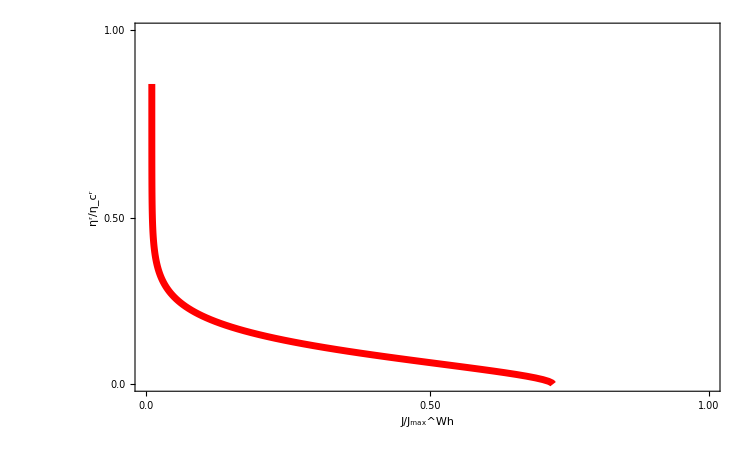

```mathematica
data2=Import["check80.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data2},Frame->True,PlotRange->{{-0.01,1},{0.06,1}},Frame->True,FrameTicks->{{{{0.06,"0.0"},{1,"1.00"},{0.50,"0.50"}},None},{{{-0.01,"0.0"},{1,"1.00"},{0.50,"0.50"}},None}},FrameLabel->{Style["J/J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,35]]
```

```mathematica
data1=Import["check50.dat"][[All,{4,5}]]
```

{{2.,0.756921},{2.,0.801204},{2.,0.8408},{2.,0.875714},{2.,0.905989},{2.,0.931705},{2.,0.952974},{2.,0.96994},{2.,0.982775},{2.,0.991672},{2.,0.996846},{2.,0.998524},{2.,0.996947},{2.,0.992362},{2.,0.985019},{2.,0.975169},{2.,0.963059},{2.,0.948931},{2.,0.933021},{2.,0.915553},{2.,0.896741},{2.,0.876789},{2.,0.855886},{2.,0.834209},{2.,0.811921},{2.,0.789173},{2.,0.766103},{2.,0.742834},{2.,0.71948},{2.,0.696142},{2.,0.672908},{2.,0.649859},{2.,0.627065},{2.,0.604585},{2.,0.582473},{2.,0.560772},{2.,0.539521},{2.,0.518751},{2.,0.498487},{2.,0.478749},{2.,0.459554},{2.,0.440911},{2.,0.422829},{2.,0.405311},{2.,0.38836},{2.,0.371974},{2.,0.356148},{2.,0.340879},{2.,0.326158},{2.,0.311976},{2.,0.298325},{2.,0.285192},{2.,0.272567},{2.,0.260437},{2.,0.24879},{2.,0.237611},{2.,0.226887},{2.,0.216605},{2.,0.20675},{2.,0.197309},{2.,0.188268},{2.,0.179613},{2.,0.17133},{2.,0.163406},{2.,0.155827},{2.,0.148581},{2.,0.141655},{2.,0.135037},{2.,0.128714},{2.,0.122674},{2.,0.116906},{2.,0.111399},{2.,0.106143},{2.,0.101126},{2.,0.0963381},{2.,0.0917704},{2.,0.087413},{2.,0.0832569},{2.,0.0792933},{2.,0.0755139},{2.,0.0719104},{2.,0.0684752},{2.,0.0652006},{2.,0.0620796},{2.,0.0591052},{2.,0.0562708},{2.,0.0535701},{2.,0.0509969},{2.,0.0485455},{2.,0.0462102},{2.,0.0439858},{2.,0.041867},{2.,0.0398491},{2.,0.0379273},{2.,0.0360972},{2.,0.0343545},{2.,0.0326951},{2.,0.031115},{2.,0.0296107},{2.,0.0281785},{2.,0.026815},{2.,0.0255169},{2.,0.0242813},{2.,0.0231051},{2.,0.0219854},{2.,0.0209197},{2.,0.0199054},{2.,0.0189399},{2.,0.0180211},{2.,0.0171465},{2.,0.0163143},{2.,0.0155222},{2.,0.0147684},{2.,0.0140511},{2.,0.0133685},{2.,0.0127189},{2.,0.0121008},{2.,0.0115126},{2.,0.0109529},{2.,0.0104203},{2.,0.00991356}}

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=Vg;
Vg=-1.1;
V=1.1;
E1=1+Vg;
E2=2+Vg;
I3[V3_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,T3_?NumericQ]:=1/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GlobalAdaptive"];
I4=FindRoot[{I3[V3,T3]==0,J3[V3,T3]==0},{{V3,Vg},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
V3=V3/.I4[[1]];
T3=T3/.I4[[2]];
I1=(2ec)/h NIntegrate[(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=2/h NIntegrate[(G+V)(T12(f1-f2)+T13(f1-f3)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
P/(2*0.316493)
2*η
```

0.991672

0.403961

```mathematica
(*T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);*)
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=3.7;
SetSharedVariable[list1]
list1={};
ParallelDo[{
E1=1+Vg;
I1=(2ec)/h NIntegrate[(TX(f1-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
J1=2/h NIntegrate[(G+V)(TX(f1-f2)),{G,-∞,∞},MaxRecursion->1000,AccuracyGoal->20,Method->"GaussKronrodRule"];
P=V*I1;
η=P/J1;
list=AppendTo[list1,{Vg,P/(2*0.316493),2*η}];
},{Vg,-10,20,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check3.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{5.14286,Null}

check3.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

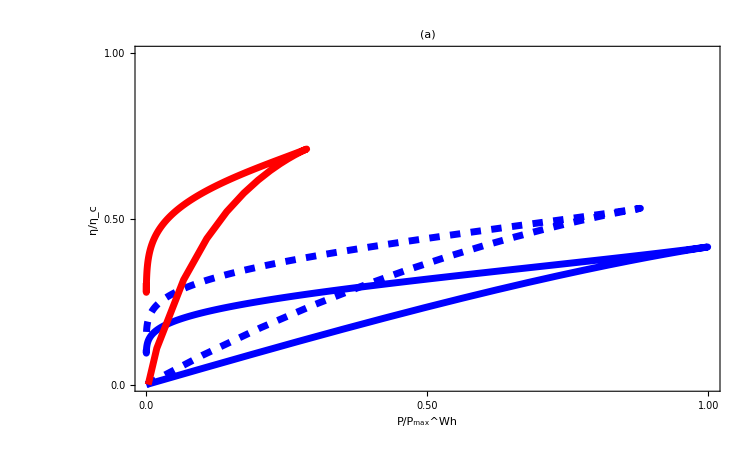

```mathematica
data1=Import["check1.dat"][[All,{2,3}]];
data2=Import["check2.dat"][[All,{2,3}]];
data3=Import["check3.dat"][[All,{2,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max^Wh",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Blue,AbsoluteDashing[7.5]],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750,LabelStyle->Directive[Bold,Black,35],PlotLabel->Style["(a)"]]
```

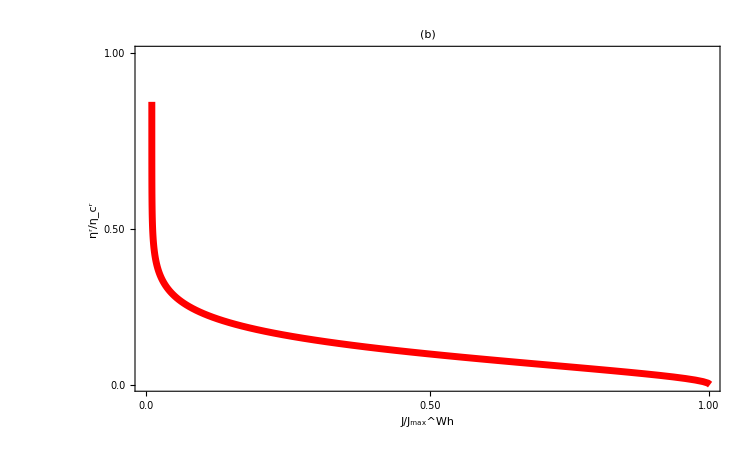

```mathematica
data2=Import["check60.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data2},Frame->True,PlotRange->{{-0.01,1},{0.06,1}},Frame->True,FrameTicks->{{{{0.06,"0.0"},{1,"1.00"},{0.50,"0.50"}},None},{{{-0.01,"0.0"},{1,"1.00"},{0.50,"0.50"}},None}},FrameLabel->{Style["J/J_max^Wh",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750,LabelStyle->Directive[Bold,Black,35],PlotLabel->Style["(b)"]]
```

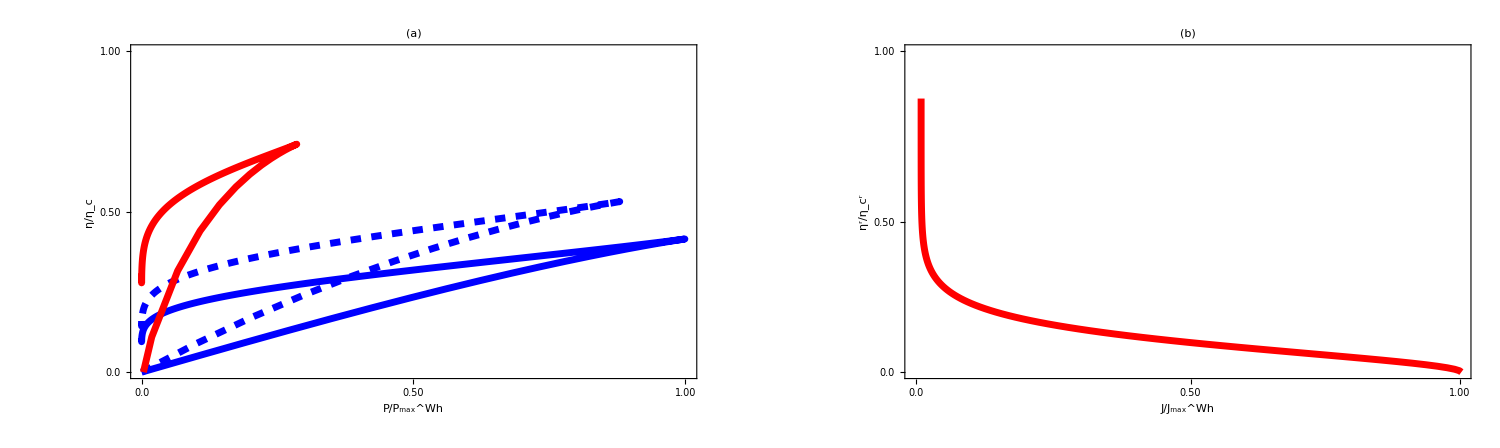

```mathematica
A5=GraphicsGrid[{{A1,A2}},ImageSize->1500]
```

# Numerical estimate of U and V_g in 2T QH Setup

```mathematica
kb=1;
h=1;
ec=1;
μ=0;
T=1/(1+Exp[-2π(G-1)/0.1]);
V1=V;
V2=0;
Gd=1;
V=0.57;
T1=2;
T2=1;
f1=1/(1+Exp[(G+ec*V1)/(kb*T1)]);
f2=1/(1+Exp[(G+ec*V2)/(kb*T2)]);
kbT=1;
df=(ⅇ^(G/kbT)/((1+ⅇ^(G/kbT))^2 kbT));
D11vu=1/0.1*NIntegrate[df*ArcSinh[√(10/(2(G-1)))](1-T/2),{G,1,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+1/0.1*NIntegrate[df*ArcCosh[√(10/(2(1-G)))](1-T/2),{G,-4,1},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
D21vu=1/0.1*NIntegrate[df*(ArcSinh[√(10/(2(G-1)))]*T)/2,{G,1,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+1/0.1*NIntegrate[df*(ArcCosh[√(10/(2(1-G)))]*T)/2,{G,-4,1},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
D11eu=1/0.1*NIntegrate[df*ArcSinh[√(10/(2(G-1)))]G(1-T/2),{G,1,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+1/0.1*NIntegrate[df*ArcCosh[√(10/(2(1-G)))]G(1-T/2),{G,-4,1},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
D21eu=1/0.1*NIntegrate[df*(ArcSinh[√(10/(2(G-1)))]*T*G)/2,{G,1,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+1/0.1*NIntegrate[df*(ArcCosh[√(10/(2(1-G)))]*T*G)/2,{G,-4,1},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
D1v=(D11vu+D21vu);
D1e=D11eu+D21eu;
u1=D1v/(2(0.01+(D1v)))
z1=D1e/(2(0.01+(D1v)))
ug=0.01/(0.01+(D1v))
U=-u1*V+z1*1
Vg=-U/ug
```

0.49964

0.238339

0.000720444

-0.046456

64.4824

# Numerical estimate of U and V_g in 3T QH Setup with voltage-temperature probe

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=1.14;
Vg=0;
E1=1+U;
E2=1;
I3[V3_?NumericQ,U_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,U_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
I4[U_]:=V3/.FindRoot[{I3[V3,U,T3]==0,J3[V3,U,T3]==0},{{V3,V},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
I5[U_]:=T3/.FindRoot[{I3[V3,U,T3]==0,J3[V3,U,T3]==0},{{V3,V},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
A11[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))(1/(1+Exp[-2π(G-1)/(hb*ω)])))/2 1/(1+Exp[(G-ec*V2)/(kb*T2)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))(1-1/(1+Exp[-2π(G-1)/(hb*ω)])))/2 1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Sinh[√(10/(2(G-1-U)))])^-1;
A12[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))(1/(1+Exp[-2π(G-1)/(hb*ω)])))/2 1/(1+Exp[(G-ec*V2)/(kb*T2)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))(1-1/(1+Exp[-2π(G-1)/(hb*ω)])))/2 1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Cosh[√(10/(2(1+U-G)))])^-1;
A1[U_?NumericQ]:=NIntegrate[A11[U,G,I4[U],I5[U]],{G,1+U,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+NIntegrate[A12[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
A2=FindRoot[A1[U]==0.01*(U-Vg),{U,0}];
A3=U/.A2[[1]];
A21[U_,G_,V3_,T3_]:=2/(0.1*3.14)(((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)(1/(1+Exp[-2π(G-1)/(hb*ω)]))1/(1+Exp[(G-ec*V2)/(kb*T2)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)(1-1/(1+Exp[-2π(G-1)/(hb*ω)]))1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Sinh[√(10/(2(G-1-U)))])^-1;
A22[U_,G_,V3_,T3_]:=2/(0.1*3.14)(((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)(1/(1+Exp[-2π(G-1)/(hb*ω)]))1/(1+Exp[(G-ec*V2)/(kb*T2)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)(1-1/(1+Exp[-2π(G-1)/(hb*ω)]))1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Cosh[√(10/(2(1+U-G)))])^-1;
A4[U_?NumericQ]:=1/3.14 NIntegrate[A21[U,G,I4[U],I5[U]],{G,1+U,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+1/3.14 NIntegrate[A22[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
A5=FindRoot[A4[U]==0.01(U-Vg),{U,0}];
A6=U/.A5[[1]];
A3
A6
A7=(A3+A6)/2
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.1153×10^-14 and 1.28587×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.86967×10^-14 and 4.43354×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.1153×10^-14 and 1.28587×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
T31=TX;
T32=TY(1-TX);
T12=TX*TY;
T13=TX(1-TY);
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=1.14;
Vg=0;
E1=1;
E2=1+U;
I3[V3_?NumericQ,U_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,U_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
I4[U_]:=V3/.FindRoot[{I3[V3,U,T3]==0,J3[V3,U,T3]==0},{{V3,V},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
I5[U_]:=T3/.FindRoot[{I3[V3,U,T3]==0,J3[V3,U,T3]==0},{{V3,V},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
A11[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2 1/(1+Exp[(G-ec*V2)/(kb*T2)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Sinh[√(10/(2(G-1-U)))])^-1;
A12[U_,G_,V3_,T3_]:=2/(0.1*3.14)(((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V2)/(kb*T2)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Cosh[√(10/(2(1+U-G)))])^-1;
A1[U_?NumericQ]:=NIntegrate[A11[U,G,I4[U],I5[U]],{G,1+U,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+NIntegrate[A12[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
A2=FindRoot[A1[U]==0.01(U-Vg),{U,0}];
A3=U/.A2[[1]];
A21[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1-1/(1+Exp[-2π(G-1-U)/(hb*ω)]))1/(1+Exp[(G-ec*V2)/(kb*T2)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Sinh[√(10/(2(G-1-U)))])^-1;
A22[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1-1/(1+Exp[-2π(G-1-U)/(hb*ω)]))1/(1+Exp[(G-ec*V2)/(kb*T2)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Cosh[√(10/(2(1+U-G)))])^-1;
A4[U_?NumericQ]:=NIntegrate[A21[U,G,I4[U],I5[U]],{G,1+U,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+NIntegrate[A22[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
A5=FindRoot[A4[U]==0.01(U-Vg),{U,0}];
A6=U/.A5[[1]];
A3
A4
(A3+A4)/2
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.03975×10^-13 and 8.71427×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.03975×10^-13 and 8.71427×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.03975×10^-13 and 8.71427×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.03975×10^-13 and 8.71427×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.03975×10^-13 and 8.71427×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.03975×10^-13 and 8.71427×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

-0.948125

5.82959

# Numerical estimate of U and V_g in 2T QSH Setup

```mathematica
kb=1;
h=1;
ec=1;
μ=0;
T=1/(1+Exp[-2π(G-1)/0.1]);
V1=V;
V2=0;
Gd=1;
V=2.52;
T1=2;
T2=1;
f1=1/(1+Exp[(G+ec*V1)/(kb*T1)]);
f2=1/(1+Exp[(G+ec*V2)/(kb*T2)]);
kbT=1;
df=(ⅇ^(G/kbT)/((1+ⅇ^(G/kbT))^2 kbT));
D11vu=1/0.1*NIntegrate[df*ArcSinh[√(10/(2(G-1)))](1-T/2),{G,1,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+1/0.1*NIntegrate[df*ArcCosh[√(10/(2(1-G)))](1-T/2),{G,-4,1},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
D21vu=1/0.1*NIntegrate[df*(ArcSinh[√(10/(2(G-1)))]*T)/2,{G,1,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+1/0.1*NIntegrate[df*(ArcCosh[√(10/(2(1-G)))]*T)/2,{G,-4,1},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
D11eu=1/0.1*NIntegrate[df*ArcSinh[√(10/(2(G-1)))]G(1-T/2),{G,1,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+1/0.1*NIntegrate[df*ArcCosh[√(10/(2(1-G)))]G(1-T/2),{G,-4,1},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
D21eu=1/0.1*NIntegrate[df*(ArcSinh[√(10/(2(G-1)))]*T*G)/2,{G,1,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+1/0.1*NIntegrate[df*(ArcCosh[√(10/(2(1-G)))]*T*G)/2,{G,-4,1},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
D1v=D11vu+D21vu;
D1e=D11eu+D21eu;
u1=D1v/(0.01+(D1v))
z1=D1e/(0.01+(D1v))
ug=0.01/(0.01+(D1v))
U=-u1*V+z1*1
Vg=-U/ug
```

0.99928

0.476677

0.000720444

-2.04151

2833.68

# Numerical estimate of U and V_g in 3T QSH setup with voltage-temperature probe

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=1.14;
Vg=0;
E1=1+U;
E2=1;
I3[V3_?NumericQ,U_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,U_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
I4[U_]:=V3/.FindRoot[{I3[V3,U,T3]==0,J3[V3,U,T3]==0},{{V3,V},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
I5[U_]:=T3/.FindRoot[{I3[V3,U,T3]==0,J3[V3,U,T3]==0},{{V3,V},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
A11u[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))(1/(1+Exp[-2π(G-1)/(hb*ω)])))/2 1/(1+Exp[(G-ec*V2)/(kb*T2)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))(1-1/(1+Exp[-2π(G-1)/(hb*ω)])))/2 1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Sinh[√(10/(2(G-1-U)))])^-1;
A11d[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))(1/(1+Exp[-2π(G-1)/(hb*ω)])))/2 1/(1+Exp[(G-ec*V2)/(kb*T2)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))(1-1/(1+Exp[-2π(G-1)/(hb*ω)])))/2 1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Sinh[√(10/(2(G-1-U)))])^-1;
A12u[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))(1/(1+Exp[-2π(G-1)/(hb*ω)])))/2 1/(1+Exp[(G-ec*V2)/(kb*T2)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))(1-1/(1+Exp[-2π(G-1)/(hb*ω)])))/2 1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Cosh[√(10/(2(G-1-U)))])^-1;
A12d[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))(1/(1+Exp[-2π(G-1)/(hb*ω)])))/2 1/(1+Exp[(G-ec*V2)/(kb*T2)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))(1-1/(1+Exp[-2π(G-1)/(hb*ω)])))/2 1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Cosh[√(10/(2(G-1-U)))])^-1;
A1u[U_?NumericQ]:=NIntegrate[A11u[U,G,I4[U],I5[U]],{G,1+U,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+NIntegrate[A12u[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
A2u=FindRoot[A1u[U]==0.01(U-Vg),{U,0}];
A3u=U/.A2u[[1]];
A1d[U_?NumericQ]:=NIntegrate[A11d[U,G,I4[U],I5[U]],{G,1+U,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+NIntegrate[A12d[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
A2d=FindRoot[A1d[U]==0.01(U-Vg),{U,0}];
A3d=U/.A2d[[1]];
A21u[U_,G_,V3_,T3_]:=2/(0.1*3.14)(((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)(1/(1+Exp[-2π(G-1)/(hb*ω)]))1/(1+Exp[(G-ec*V2)/(kb*T2)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)(1-1/(1+Exp[-2π(G-1)/(hb*ω)]))1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Sinh[√(10/(2(G-1-U)))])^-1;
A21d[U_,G_,V3_,T3_]:=2/(0.1*3.14)(((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Sinh[√(10/(2(G-1-U)))])^-1;
A22u[U_,G_,V3_,T3_]:=2/(0.1*3.14)(((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)(1/(1+Exp[-2π(G-1)/(hb*ω)]))1/(1+Exp[(G-ec*V2)/(kb*T2)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)(1-1/(1+Exp[-2π(G-1)/(hb*ω)]))1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Cosh[√(10/(2(G-1-U)))])^-1;
A22d[U_,G_,V3_,T3_]:=2/(0.1*3.14)(((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Cosh[√(10/(2(G-1-U)))])^-1;
A4u[U_?NumericQ]:=NIntegrate[A21u[U,G,I4[U],I5[U]],{G,1+U,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+NIntegrate[A22u[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
A5u=FindRoot[A4u[U]==0.01(U-Vg),{U,0}];
A6u=U/.A5u[[1]];
A4d[U_?NumericQ]:=NIntegrate[A21d[U,G,I4[U],I5[U]],{G,1+U,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+NIntegrate[A22d[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
A5d=FindRoot[A4d[U]==0.01(U-Vg),{U,0}];
A6d=U/.A5d[[1]];
A3u
A3d
A6u
A6d
U1=(A3u+A3d+A6u+A6d)/2
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.25858×10^-12 and 1.59664×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.25858×10^-12 and 1.59664×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
T31u=TX;
T31d=TX(1-TY);
T32u=TY(1-TX);
T32d=TY;
T12u=TX*TY;
T12d=0;
T13u=TX(1-TY);
T13d=TX;
T31=T31u+T31d;
T32=T32u+T32d;
T12=T12u+T12d;
T13=T13u+T13d;
ec=1;
a=1;
kb=1;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
V1=-V;
V2=0;
T1=2;
T2=1;
Vg=0;
f2=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3=1/(1+Exp[(G-ec*V3)/(kb*T3)]);
ω=0.1;
h=1;
hb=1;
V=2.7;
E1=1;
E2=1+U;
I3[V3_?NumericQ,U_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
J3[V3_?NumericQ,U_?NumericQ,T3_?NumericQ]:=ec/h NIntegrate[(G)(T31(f3-f1)+T32(f3-f2)),{G,-∞,∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
I4[U_]:=V3/.FindRoot[{I3[V3,U,T3]==0,J3[V3,U,T3]==0},{{V3,V},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
I5[U_]:=T3/.FindRoot[{I3[V3,U,T3]==0,J3[V3,U,T3]==0},{{V3,V},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
A11u[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2 1/(1+Exp[(G-ec*V2)/(kb*T2)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Sinh[√(10/(2(G-1-U)))])^-1;
A11d[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)((1/(1+Exp[-2π(G-1)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2 1/(1+Exp[(G-ec*V2)/(kb*T2)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)(1-(1/(1+Exp[-2π(G-1)/(hb*ω)])))1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Sinh[√(10/(2(G-1-U)))])^-1;
A12u[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2 1/(1+Exp[(G-ec*V2)/(kb*T2)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Cosh[√(10/(2(G-1-U)))])^-1;
A12d[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)((1/(1+Exp[-2π(G-1)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2 1/(1+Exp[(G-ec*V2)/(kb*T2)])+(1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)(1-(1/(1+Exp[-2π(G-1)/(hb*ω)])))1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Cosh[√(10/(2(G-1-U)))])^-1;
A1u[U_?NumericQ]:=NIntegrate[A11u[U,G,I4[U],I5[U]],{G,1+U,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+NIntegrate[A12u[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
A2u=FindRoot[A1u[U]==0.01(U-Vg),{U,0}];
A3u=U/.A2u[[1]];
A1d[U_?NumericQ]:=NIntegrate[A11d[U,G,I4[U],I5[U]],{G,1+U,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+NIntegrate[A12d[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
A2d=FindRoot[A1d[U]==0.01(U-Vg),{U,0}];
A3d=U/.A2d[[1]];
A21u[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V2)/(kb*T2)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Sinh[√(10/(2(G-1-U)))])^-1;
A21d[U_,G_,V3_,T3_]:=2/(0.1*3.14)((((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))(1/(1+Exp[-2π(G-1)/(hb*ω)])))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+(1-1/(2(1+Exp[-2π(G-1-U)/(hb*ω)])))1/(1+Exp[(G-ec*V2)/(kb*T2)])+(((1-1/(1+Exp[-2π(G-1)/(hb*ω)]))(1/(1+Exp[-2π(G-1-U)/(hb*ω)])))/2)1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Sinh[√(10/(2(G-1-U)))])^-1;
A22u[U_,G_,V3_,T3_]:=2/(0.1*3.14)((1-(1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V2)/(kb*T2)])+((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))/2)1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Cosh[√(10/(2(G-1-U)))])^-1;
A22d[U_,G_,V3_,T3_]:=2/(0.1*3.14)((((1/(1+Exp[-2π(G-1-U)/(hb*ω)]))(1/(1+Exp[-2π(G-1)/(hb*ω)])))/2)1/(1+Exp[(G-ec*V1)/(kb*T1)])+(1-1/(2(1+Exp[-2π(G-1-U)/(hb*ω)])))1/(1+Exp[(G-ec*V2)/(kb*T2)])+(((1-1/(1+Exp[-2π(G-1)/(hb*ω)]))(1/(1+Exp[-2π(G-1-U)/(hb*ω)])))/2)1/(1+Exp[(G-ec*V3)/(kb*T3)])-1/(1+Exp[G]))(Cosh[√(10/(2(G-1-U)))])^-1;
A4u[U_?NumericQ]:=NIntegrate[A21u[U,G,I4[U],I5[U]],{G,1+U,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+NIntegrate[A22u[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
A5u=FindRoot[A4u[U]==0.01(U-Vg),{U,0}];
A6u=U/.A5u[[1]];
A4d[U_?NumericQ]:=NIntegrate[A21d[U,G,I4[U],I5[U]],{G,1+U,+∞},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20]+NIntegrate[A22d[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->1000,AccuracyGoal->20];
A5d=FindRoot[A4d[U]==0.01(U-Vg)==0,{U,0}];
A6d=U/.A5d[[1]];
A3u
A3d
A6u
A6d
U1=(A3u+A3d+A6u+A6d)/2
```

```mathematica
2.77536*10^-7
```

2.77536×10^-7

```mathematica
NumberForm[2.77536*^-7,{6,5}]
```

2.77536×10^-7

```mathematica
NumberForm[2.77536*^-7,16]
```

2.77536×10^-7

```mathematica
RealDigits[2.77536*^-7]
```

{{2,7,7,5,3,5,9,9,9,9,9,9,9,9,9,9},-6}

```mathematica
(*Define functions and parameters*)TX[G_]:=1/(1+Exp[-2 π (G-E1)/(hb*ω)]);
TY[G_]:=1/(1+Exp[-2 π (G-E2)/(hb*ω)]);

T31u[G_,TX_,TY_]:=TX (1-TY);
T31d[G_,TX_,TY_]:=TX (1-TY);
T32u[G_,TX_,TY_]:=TY (1-TX);
T32d[G_,TX_,TY_]:=TY;
T12u[G_,TX_,TY_]:=TX*TY;
T12d[G_,TX_,TY_]:=0;
T13u[G_,TX_,TY_]:=TX (1-TY);
T13d[G_,TX_,TY_]:=TX;

T31[G_,TX_,TY_]:=T31u[G,TX,TY]+T31d[G,TX,TY];
T32[G_,TX_,TY_]:=T32u[G,TX,TY]+T32d[G,TX,TY];
T12[G_,TX_,TY_]:=T12u[G,TX,TY]+T12d[G,TX,TY];
T13[G_,TX_,TY_]:=T13u[G,TX,TY]+T13d[G,TX,TY];

(*Parameters*)
ec=1;
a=1;
kb=1;
ω=0.1;
hb=1;
h=1;
V=1.14;
Vg=0;
E1=1+U;
E2=1;
V1=-V;
V2=0;
T1=2;
T2=1;

f2[G_]:=1/(1+Exp[(G-ec*V2)/(kb*T2)]);
f1[G_]:=1/(1+Exp[(G-ec*V1)/(kb*T1)]);
f3[G_]:=1/(1+Exp[(G-ec*V3)/(kb*T3)]);

(*Define integral functions*)
I3[V3_?NumericQ,U_?NumericQ,T3_?NumericQ]:=ec/h Parallelize[NIntegrate[(T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G])),{G,-10,10},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->10]];

J3[V3_?NumericQ,U_?NumericQ,T3_?NumericQ]:=ec/h Parallelize[NIntegrate[(G (T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G]))),{G,-10,10},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->10]];
I4[U_]:=V3/.FindRoot[{I3[V3,U,T3]==0,J3[V3,U,T3]==0},{{V3,V},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
I5[U_]:=T3/.FindRoot[{I3[V3,U,T3]==0,J3[V3,U,T3]==0},{{V3,V},{T3,2*T2}},AccuracyGoal->4,PrecisionGoal->4];
(*Define A functions*)
A11u[U_,G_,V3_,T3_]:=2/(0.1*3.14) ((1-1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) f1[G]+((1/(1+Exp[-2 π (G-1-U)/(hb*ω)])) (1/(1+Exp[-2 π (G-1)/(hb*ω)])))/2 f2[G]+((1/(1+Exp[-2 π (G-1-U)/(hb*ω)])) (1-1/(1+Exp[-2 π (G-1)/(hb*ω)])))/2 f3[G]-1/(1+Exp[G])) (Sinh[Sqrt[10/(2 (G-1-U))]])^-1;

A11d[U_,G_,V3_,T3_]:=2/(0.1*3.14) ((1-1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) f1[G]+((1/(1+Exp[-2 π (G-1-U)/(hb*ω)])) (1/(1+Exp[-2 π (G-1)/(hb*ω)])))/2 f2[G]+((1/(1+Exp[-2 π (G-1-U)/(hb*ω)])) (1-1/(1+Exp[-2 π (G-1)/(hb*ω)])))/2 f3[G]-1/(1+Exp[G])) (Sinh[Sqrt[10/(2 (G-1-U))]])^-1;

A12u[U_,G_,V3_,T3_]:=2/(0.1*3.14) ((1-1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) f1[G]+((1/(1+Exp[-2 π (G-1-U)/(hb*ω)])) (1/(1+Exp[-2 π (G-1)/(hb*ω)])))/2 f2[G]+((1/(1+Exp[-2 π (G-1-U)/(hb*ω)])) (1-1/(1+Exp[-2 π (G-1)/(hb*ω)])))/2 f3[G]-1/(1+Exp[G])) (Cosh[Sqrt[10/(2 (G-1-U))]])^-1;

A12d[U_,G_,V3_,T3_]:=2/(0.1*3.14) ((1-1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) f1[G]+((1/(1+Exp[-2 π (G-1-U)/(hb*ω)])) (1/(1+Exp[-2 π (G-1)/(hb*ω)])))/2 f2[G]+((1/(1+Exp[-2 π (G-1-U)/(hb*ω)])) (1-1/(1+Exp[-2 π (G-1)/(hb*ω)])))/2 f3[G]-1/(1+Exp[G])) (Cosh[Sqrt[10/(2 (G-1-U))]])^-1;

(*Parallelized Integration Functions*)
A1u[U_?NumericQ]:=Parallelize[NIntegrate[A11u[U,G,I4[U],I5[U]],{G,1+U,10},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->10]+NIntegrate[A12u[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->10]];

A1d[U_?NumericQ]:=Parallelize[NIntegrate[A11d[U,G,I4[U],I5[U]],{G,1+U,10},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->10]+NIntegrate[A12d[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->10]];

A21u[U_,G_,V3_,T3_]:=2/(0.1*3.14) ((1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) f1[G]+(1-1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) (1/(1+Exp[-2 π (G-1)/(hb*ω)])) f2[G]+(1-1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) (1-1/(1+Exp[-2 π (G-1)/(hb*ω)])) f3[G]-1/(1+Exp[G])) (Sinh[Sqrt[10/(2 (G-1-U))]])^-1;

A21d[U_,G_,V3_,T3_]:=2/(0.1*3.14) ((1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) f1[G]+(1-1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) (1/(1+Exp[-2 π (G-1)/(hb*ω)])) f2[G]+(1-1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) (1-1/(1+Exp[-2 π (G-1)/(hb*ω)])) f3[G]-1/(1+Exp[G])) (Sinh[Sqrt[10/(2 (G-1-U))]])^-1;

A22u[U_,G_,V3_,T3_]:=2/(0.1*3.14) ((1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) f1[G]+(1-1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) (1/(1+Exp[-2 π (G-1)/(hb*ω)])) f2[G]+(1-1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) (1-1/(1+Exp[-2 π (G-1)/(hb*ω)])) f3[G]-1/(1+Exp[G])) (Cosh[Sqrt[10/(2 (G-1-U))]])^-1;

A22d[U_,G_,V3_,T3_]:=2/(0.1*3.14) ((1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) f1[G]+(1-1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) (1/(1+Exp[-2 π (G-1)/(hb*ω)])) f2[G]+(1-1/(1+Exp[-2 π (G-1-U)/(hb*ω)])/2) (1-1/(1+Exp[-2 π (G-1)/(hb*ω)])) f3[G]-1/(1+Exp[G])) (Cosh[Sqrt[10/(2 (G-1-U))]])^-1;

(*Parallelized Integration Functions*)
A2u[U_?NumericQ]:=Parallelize[NIntegrate[A21u[U,G,I4[U],I5[U]],{G,1+U,10},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->10]+NIntegrate[A22u[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->10]];

A2d[U_?NumericQ]:=Parallelize[NIntegrate[A21d[U,G,I4[U],I5[U]],{G,1+U,10},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->10]+NIntegrate[A22d[U,G,I4[U],I5[U]],{G,U-4,1+U},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->10]];

(*Example usage*)
resultA1u=A1u[1];
resultA1d=A1d[1];
resultA2u=A2u[1];
resultA2d=A2d[1];

Print["A1u result: ",resultA1u]
Print["A1d result: ",resultA1d]
Print["A2u result: ",resultA2u]
Print["A2d result: ",resultA2d]
```

Parallelize::nopar1: NIntegrate[A11u[1,G,I4[1],I5[1]],{G,1+1,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10]+NIntegrate[A12u[1,G,I4[1],I5[1]],{G,1-4,1+1},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

Parallelize::nopar1: NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G]),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

NIntegrate::inumr: The integrand (2 (1-1/(1+ⅇ^Times[«2»])) (1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^Times[«2»])))/(1+ⅇ^(-62.8319 (-1+G+Times[«2»])))+(1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^G)) (1/(1+ⅇ^(-62.8319 Plus[«2»]))+(1-1/Plus[«2»])/(1+ⅇ^Times[«2»])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-10,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Parallelize::nopar1: NIntegrate[G (T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G])),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::nopar1 will be suppressed during this calculation.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Parallelize::nopar1: NIntegrate[A11d[1,G,I4[1],I5[1]],{G,1+1,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10]+NIntegrate[A12d[1,G,I4[1],I5[1]],{G,1-4,1+1},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

Parallelize::nopar1: NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G]),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

NIntegrate::inumr: The integrand (2 (1-1/(1+ⅇ^Times[«2»])) (1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^Times[«2»])))/(1+ⅇ^(-62.8319 (-1+G+Times[«2»])))+(1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^G)) (1/(1+ⅇ^(-62.8319 Plus[«2»]))+(1-1/Plus[«2»])/(1+ⅇ^Times[«2»])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-10,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Parallelize::nopar1: NIntegrate[G (T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G])),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::nopar1 will be suppressed during this calculation.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Parallelize::nopar1: NIntegrate[A21u[1,G,I4[1],I5[1]],{G,1+1,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10]+NIntegrate[A22u[1,G,I4[1],I5[1]],{G,1-4,1+1},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

Parallelize::nopar1: NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G]),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

NIntegrate::inumr: The integrand (2 (1-1/(1+ⅇ^Times[«2»])) (1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^Times[«2»])))/(1+ⅇ^(-62.8319 (-1+G+Times[«2»])))+(1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^G)) (1/(1+ⅇ^(-62.8319 Plus[«2»]))+(1-1/Plus[«2»])/(1+ⅇ^Times[«2»])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-10,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Parallelize::nopar1: NIntegrate[G (T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G])),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::nopar1 will be suppressed during this calculation.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Parallelize::nopar1: NIntegrate[A21d[1,G,I4[1],I5[1]],{G,1+1,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10]+NIntegrate[A22d[1,G,I4[1],I5[1]],{G,1-4,1+1},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

Parallelize::nopar1: NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G]),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

NIntegrate::inumr: The integrand (2 (1-1/(1+ⅇ^Times[«2»])) (1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^Times[«2»])))/(1+ⅇ^(-62.8319 (-1+G+Times[«2»])))+(1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^G)) (1/(1+ⅇ^(-62.8319 Plus[«2»]))+(1-1/Plus[«2»])/(1+ⅇ^Times[«2»])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-10,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Parallelize::nopar1: NIntegrate[G (T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G])),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::nopar1 will be suppressed during this calculation.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Parallelize::nopar1: NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G]),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

NIntegrate::inumr: The integrand (2 (1-1/(1+ⅇ^Times[«2»])) (1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^Times[«2»])))/(1+ⅇ^(-62.8319 (-1+G+Times[«2»])))+(1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^G)) (1/(1+ⅇ^(-62.8319 Plus[«2»]))+(1-1/Plus[«2»])/(1+ⅇ^Times[«2»])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-10,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Parallelize::nopar1: NIntegrate[G (T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G])),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Parallelize::nopar1: NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G]),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::nopar1 will be suppressed during this calculation.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

A1u result: 0.348003+NIntegrate[A12u[1,G,I4[1],I5[1]],{G,1-4,1+1},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10]

Parallelize::nopar1: NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G]),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

NIntegrate::inumr: The integrand (2 (1-1/(1+ⅇ^Times[«2»])) (1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^Times[«2»])))/(1+ⅇ^(-62.8319 (-1+G+Times[«2»])))+(1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^G)) (1/(1+ⅇ^(-62.8319 Plus[«2»]))+(1-1/Plus[«2»])/(1+ⅇ^Times[«2»])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-10,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Parallelize::nopar1: NIntegrate[G (T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G])),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Parallelize::nopar1: NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G]),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::nopar1 will be suppressed during this calculation.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

A1d result: 0.348003+NIntegrate[A12d[1,G,I4[1],I5[1]],{G,1-4,1+1},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10]

Parallelize::nopar1: NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G]),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

NIntegrate::inumr: The integrand (2 (1-1/(1+ⅇ^Times[«2»])) (1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^Times[«2»])))/(1+ⅇ^(-62.8319 (-1+G+Times[«2»])))+(1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^G)) (1/(1+ⅇ^(-62.8319 Plus[«2»]))+(1-1/Plus[«2»])/(1+ⅇ^Times[«2»])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-10,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Parallelize::nopar1: NIntegrate[G (T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G])),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Parallelize::nopar1: NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G]),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::nopar1 will be suppressed during this calculation.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

A2u result: 0.348002+NIntegrate[A22u[1,G,I4[1],I5[1]],{G,1-4,1+1},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10]

Parallelize::nopar1: NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G]),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

NIntegrate::inumr: The integrand (2 (1-1/(1+ⅇ^Times[«2»])) (1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^Times[«2»])))/(1+ⅇ^(-62.8319 (-1+G+Times[«2»])))+(1/(1+ⅇ^(0.5 Plus[«2»]))-1/(1+ⅇ^G)) (1/(1+ⅇ^(-62.8319 Plus[«2»]))+(1-1/Plus[«2»])/(1+ⅇ^Times[«2»])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-10,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Parallelize::nopar1: NIntegrate[G (T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G])),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Parallelize::nopar1: NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-f1[G])+T32[G,TX[G],TY[G]] (f3[G]-f2[G]),{G,-10,10},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10] cannot be parallelized; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::nopar1 will be suppressed during this calculation.

FindRoot::nlnum: The function value {NIntegrate[T31[G,TX[G],TY[G]] (f3[G]-1. f1[G])+T32[G,TX[G],TY[G]] (f3[G]-1. f2[G]),{G,-10.,10.},Method→GlobalAdaptive,MaxRecursion→20.,AccuracyGoal→10.],0.} is not a list of numbers with dimensions {2} at {V3,T3} = {1.14,2.}.

ReplaceAll::reps: {FindRoot[{I3[V3,1,T3]==0,J3[V3,1,T3]==0},{{V3,V},{T3,2 T2}},AccuracyGoal→4,PrecisionGoal→4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

A2d result: 0.348002+NIntegrate[A22d[1,G,I4[1],I5[1]],{G,1-4,1+1},Method→GlobalAdaptive,MaxRecursion→20,AccuracyGoal→10]

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T12uu=TX TY;
T13uu=TX (1-TY);
T21uu=0;
T22uu=(1-TY);
T23uu=TY;
T31uu=TX;
T32uu=TY(1-TX);
T33uu=(1-TX)( 1-TY);
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
For[V=0,V<=0.84,V=V+0.01,
{E2=ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(1-T11uu)*G0*df,{G,n0,n1}];
G12=NIntegrate[(-T12uu)*G0*df,{G,n0,n1}];
G13=NIntegrate[(-T13uu)*G0*df,{G,n0,n1}];
G31=NIntegrate[(-T31uu)*G0*df,{G,n0,n1}];
G32=NIntegrate[(-T32uu)*G0*df,{G,n0,n1}];
G33=NIntegrate[(1-T33uu)*G0*df,{G,n0,n1}];
L11=NIntegrate[(1-T11uu)*(G-μ)*L0*df,{G,n0,n1}];
L12=NIntegrate[(-T12uu)*(G-μ)*L0*df,{G,n0,n1}];
L13=NIntegrate[(-T13uu)*(G-μ)*L0*df,{G,n0,n1}];
L23=NIntegrate[(-T23uu)*(G-μ)*L0*df,{G,n0,n1}];
L33=NIntegrate[(1-T33uu)*(G-μ)*L0*df,{G,n0,n1}];
L31=NIntegrate[(-T31uu)*(G-μ)*L0*df,{G,n0,n1}];
L32=NIntegrate[(-T32uu)*(G-μ)*L0*df,{G,n0,n1}];
π11=NIntegrate[(1-T11uu)*(G-μ)*Lp*df,{G,n0,n1}];
π12=NIntegrate[(-T12uu)*(G-μ)*Lp*df,{G,n0,n1}];
π13=NIntegrate[(-T13uu)*(G-μ)*Lp*df,{G,n0,n1}];
π31=NIntegrate[(-T31uu)*(G-μ)*Lp*df,{G,n0,n1}];
π33=NIntegrate[(1-T33uu)*(G-μ)*Lp*df,{G,n0,n1}];
K11=NIntegrate[(1-T11uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K12=NIntegrate[(-T12uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K13=NIntegrate[(-T13uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K31=NIntegrate[(-T31uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K32=NIntegrate[(-T32uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K33=NIntegrate[(1-T33uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,V,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z}];
}];
},{x1,0,0.84,0.1}];//AbsoluteTiming
list=Sort[list1];
Export["check20.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {0.406624}. NIntegrate obtained 1.26054×10^-19 and 4.42685×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {0.406624}. NIntegrate obtained 1.26054×10^-19 and 4.42685×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {0.406624}. NIntegrate obtained 1.26054×10^-19 and 4.42685×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{62.6104,Null}

check20.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

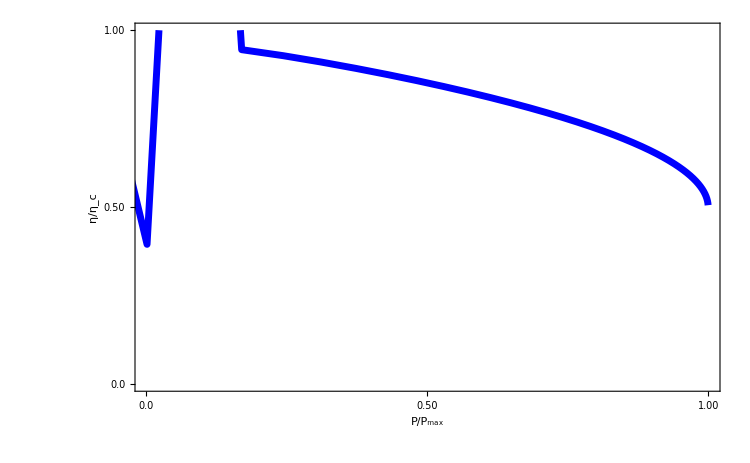

```mathematica
data2=Import["check20.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data2},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750]
```

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T12uu=TX TY;
T13uu=TX (1-TY);
T21uu=0;
T22uu=(1-TY);
T23uu=TY;
T31uu=TX;
T32uu=TY(1-TX);
T33uu=(1-TX)( 1-TY);
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
V=0.43;
Vg=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(1-T11uu)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G12=NIntegrate[(-T12uu)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G13=NIntegrate[(-T13uu)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G31=NIntegrate[(-T31uu)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G32=NIntegrate[(-T32uu)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G33=NIntegrate[(1-T33uu)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L11=NIntegrate[(1-T11uu)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L12=NIntegrate[(-T12uu)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L13=NIntegrate[(-T13uu)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L23=NIntegrate[(-T23uu)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L33=NIntegrate[(1-T33uu)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L31=NIntegrate[(-T31uu)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L32=NIntegrate[(-T32uu)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π11=NIntegrate[(1-T11uu)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π12=NIntegrate[(-T12uu)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π13=NIntegrate[(-T13uu)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π31=NIntegrate[(-T31uu)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π33=NIntegrate[(1-T33uu)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K11=NIntegrate[(1-T11uu)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K12=NIntegrate[(-T12uu)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K13=NIntegrate[(-T13uu)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K31=NIntegrate[(-T31uu)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K32=NIntegrate[(-T32uu)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K33=NIntegrate[(1-T33uu)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z}];
},{x1,44,85,1}];//AbsoluteTiming
list=Sort[list1];
Export["check20.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 100 recursive bisections in G near {G} = {1.}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 100 recursive bisections in G near {G} = {1.}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 100 recursive bisections in G near {G} = {1.}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 100 recursive bisections in G near {G} = {1.}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{10.3392,Null}

check20.dat

```mathematica
data2=Import["check20.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data2},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

-Graphics-

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

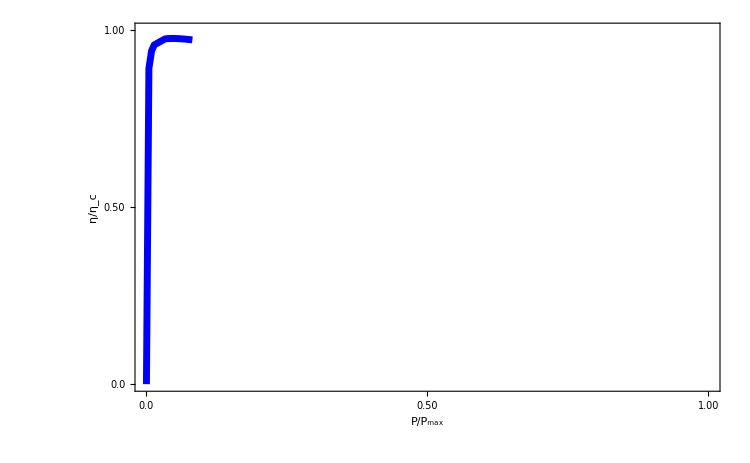

```mathematica
data2=Import["check21.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data2},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750]
```

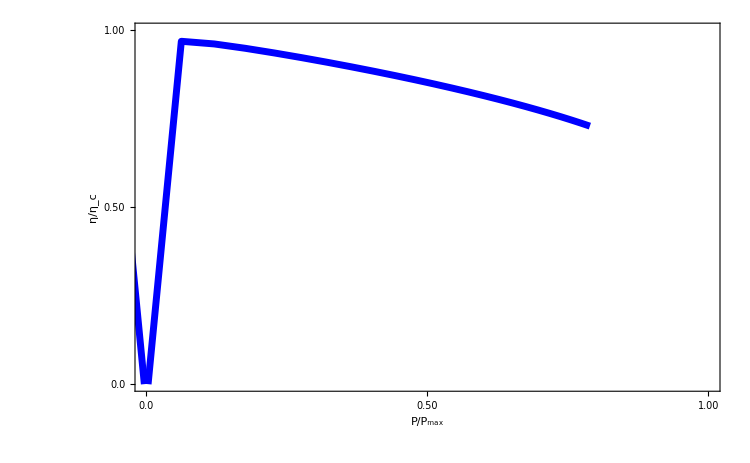

```mathematica
data2=Import["check23.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data2},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750]
```

```mathematica
kb=1;
T=1;
θ=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=x1*a/ec;
V=0.43*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z,Jq*h/(kb^2*θ*δT),Subscript[η, r]}]
},{x1,44,85,1}];//AbsoluteTiming
list=Sort[list1];
Export["check40.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {52.4935}. NIntegrate obtained 1.92135×10^-23 and 1.02755×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {55.7216}. NIntegrate obtained 9.57635×10^-25 and 4.70669×10^-27 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {61.31}. NIntegrate obtained 2.3711×10^-27 and 4.99841×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {64.876}. NIntegrate obtained 1.18155×10^-28 and 3.48723×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {43.8983}. NIntegrate obtained 1.55693×10^-19 and 1.17689×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {46.9912}. NIntegrate obtained 7.7512×10^-21 and 1.00146×10^-23 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {49.5985}. NIntegrate obtained 3.85991×10^-22 and 1.33849×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {52.4935}. NIntegrate obtained -9.4535×10^-24 and 1.90329×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {55.7216}. NIntegrate obtained -4.68711×10^-25 and 9.77127×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {58.7049}. NIntegrate obtained 4.78809×10^-26 and 9.55907×10^-28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {61.9944}. NIntegrate obtained -1.16532×10^-27 and 2.39624×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {64.876}. NIntegrate obtained -5.84381×10^-29 and 1.78591×10^-30 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {52.4935}. NIntegrate obtained -9.76001×10^-24 and 2.92582×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {61.31}. NIntegrate obtained -1.21085×10^-27 and 3.97708×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {64.876}. NIntegrate obtained -5.9717×10^-29 and 1.70132×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {43.8983}. NIntegrate obtained -7.66528×10^-20 and 6.20154×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {46.9912}. NIntegrate obtained -3.81404×10^-21 and 1.36571×10^-23 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {49.5985}. NIntegrate obtained -1.89859×10^-22 and 6.21958×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {55.7216}. NIntegrate obtained -4.88924×10^-25 and 1.44278×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {58.7049}. NIntegrate obtained -2.3486×10^-26 and 6.66067×10^-29 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {43.8983}. NIntegrate obtained -7.90399×10^-20 and 5.56739×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {46.5819}. NIntegrate obtained -3.93724×10^-21 and 1.29438×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {49.5985}. NIntegrate obtained -1.96132×10^-22 and 1.91885×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {58.7049}. NIntegrate obtained -2.43948×10^-26 and 8.893×10^-28 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {68.0079}. NIntegrate obtained 5.81028×10^-30 and 2.05298×10^-32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {70.5393}. NIntegrate obtained 2.8786×10^-31 and 1.25625×10^-32 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {79.2334}. NIntegrate obtained 3.64223×10^-35 and 3.06795×10^-36 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained 6.49312×10^-37 and 2.28068×10^-38 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {68.0079}. NIntegrate obtained -2.88211×10^-30 and 1.12051×10^-32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {70.5393}. NIntegrate obtained -1.41686×10^-31 and 8.45717×10^-33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {73.2429}. NIntegrate obtained 1.44492×10^-32 and 5.86072×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {77.1438}. NIntegrate obtained 2.68168×10^-34 and 1.33831×10^-35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {75.1489}. NIntegrate obtained 1.98118×10^-33 and 3.19607×10^-35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {79.2334}. NIntegrate obtained -1.81309×10^-35 and 1.48103×10^-36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {81.4236}. NIntegrate obtained 4.76657×10^-36 and 2.18012×10^-37 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {67.1999}. NIntegrate obtained -2.99254×10^-30 and 9.56774×10^-33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {70.5393}. NIntegrate obtained -1.46174×10^-31 and 4.10537×10^-33 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -3.15219×10^-37 and 2.06789×10^-38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {73.2429}. NIntegrate obtained -7.15685×10^-33 and 3.3407×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {77.1438}. NIntegrate obtained -1.33024×10^-34 and 6.01203×10^-36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {75.1489}. NIntegrate obtained -9.67725×10^-34 and 6.46606×10^-36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {79.2334}. NIntegrate obtained -1.82913×10^-35 and 1.58692×10^-36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {81.4236}. NIntegrate obtained -2.31739×10^-36 and 2.71492×10^-37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {83.7212}. NIntegrate obtained -3.34093×10^-37 and 2.12795×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {73.2429}. NIntegrate obtained -7.29235×10^-33 and 2.52002×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {77.1438}. NIntegrate obtained -1.35144×10^-34 and 7.37108×10^-36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {75.1489}. NIntegrate obtained -1.01346×10^-33 and 3.77428×10^-35 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {81.4236}. NIntegrate obtained -2.44921×10^-36 and 4.25248×10^-38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{9.17512,Null}

check40.dat

```mathematica
data2=Import["check40.dat"][[All,{3,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data2},Frame->True,PlotRange->{{0.0,1.001},{0,1.00}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1.00,"1.00"}},None},{{{0.50,"0.50"},{0,"0.0"},{1,"1.00"}},None}},FrameLabel->{Style["P/P_max",45,Bold,Black],Style["η/η_c",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750]
```

-Graphics-

```mathematica
kb=1;
T=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T12uu=TX TY;
T13uu=TX (1-TY);
T21uu=0;
T22uu=(1-TY);
T23uu=TY;
T31uu=TX;
T32uu=TY(1-TX);
T33uu=(1-TX)( 1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
Vg=x1*a/ec;
V=0.84*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=ec*Vg;
E1=ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(1-T11uu)*G0*df,{G,n0,n1}];
G12=NIntegrate[(-T12uu)*G0*df,{G,n0,n1}];
G13=NIntegrate[(-T13uu)*G0*df,{G,n0,n1}];
G31=NIntegrate[(-T31uu)*G0*df,{G,n0,n1}];
G32=NIntegrate[(-T32uu)*G0*df,{G,n0,n1}];
G33=NIntegrate[(1-T33uu)*G0*df,{G,n0,n1}];
L11=NIntegrate[(1-T11uu)*(G-μ)*L0*df,{G,n0,n1}];
L12=NIntegrate[(-T12uu)*(G-μ)*L0*df,{G,n0,n1}];
L13=NIntegrate[(-T13uu)*(G-μ)*L0*df,{G,n0,n1}];
L23=NIntegrate[(-T23uu)*(G-μ)*L0*df,{G,n0,n1}];
L33=NIntegrate[(1-T33uu)*(G-μ)*L0*df,{G,n0,n1}];
L31=NIntegrate[(-T31uu)*(G-μ)*L0*df,{G,n0,n1}];
L32=NIntegrate[(-T32uu)*(G-μ)*L0*df,{G,n0,n1}];
π11=NIntegrate[(1-T11uu)*(G-μ)*Lp*df,{G,n0,n1}];
π12=NIntegrate[(-T12uu)*(G-μ)*Lp*df,{G,n0,n1}];
π13=NIntegrate[(-T13uu)*(G-μ)*Lp*df,{G,n0,n1}];
π31=NIntegrate[(-T31uu)*(G-μ)*Lp*df,{G,n0,n1}];
π33=NIntegrate[(1-T33uu)*(G-μ)*Lp*df,{G,n0,n1}];
K11=NIntegrate[(1-T11uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K12=NIntegrate[(-T12uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K13=NIntegrate[(-T13uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K31=NIntegrate[(-T31uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K32=NIntegrate[(-T32uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
K33=NIntegrate[(1-T33uu)*(G-μ)^2*Lh*df,{G,n0,n1}];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
ηr1=J1/P1*0.01;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,P/P0,P1/P,η1,P1/P0,η,ηm,Pm/P0,Z,-J1/Jq,ηr1}];
},{x1,4,84,2}];//AbsoluteTiming
list=Sort[list1];
Export["check30.dat",list]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained -0.000281215 and 8.27778×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.89546}. NIntegrate obtained 0.0000454177 and 7.86841×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {15.8089}. NIntegrate obtained 1.12577×10^-7 and 8.7826×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {27.8667}. NIntegrate obtained 6.91729×10^-13 and 2.03864×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {39.9373}. NIntegrate obtained 4.2501×10^-18 and 2.09806×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained -0.000281215 and 8.27778×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.89546}. NIntegrate obtained -0.0000446958 and 6.46594×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {15.8089}. NIntegrate obtained -1.10763×10^-7 and 6.5107×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {21.975}. NIntegrate obtained 2.79063×10^-10 and 5.11612×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {28.0101}. NIntegrate obtained -6.8072×10^-13 and 1.07039×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {33.8278}. NIntegrate obtained 1.71462×10^-15 and 1.12281×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {39.9373}. NIntegrate obtained -4.18195×10^-18 and 2.59982×10^-20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {45.7835}. NIntegrate obtained 1.05298×10^-20 and 1.21848×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained -0.00112464 and 3.27638×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.89546}. NIntegrate obtained -7.21908×10^-7 and 7.22644×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {15.8089}. NIntegrate obtained -1.12577×10^-7 and 8.7826×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {21.973}. NIntegrate obtained -2.74622×10^-10 and 2.40451×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {27.8667}. NIntegrate obtained -6.91729×10^-13 and 2.03864×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {33.8278}. NIntegrate obtained -1.68733×10^-15 and 1.90965×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {39.9373}. NIntegrate obtained -4.2501×10^-18 and 2.09806×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {45.7835}. NIntegrate obtained -1.03728×10^-20 and 1.60291×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {21.9776}. NIntegrate obtained -4.48542×10^-12 and 1.79214×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.00006}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {33.8278}. NIntegrate obtained -1.71462×10^-15 and 1.12281×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {61.31}. NIntegrate obtained 1.18555×10^-27 and 2.4992×10^-30 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {51.9892}. NIntegrate obtained 2.61129×10^-23 and 5.76732×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {57.4771}. NIntegrate obtained 6.48026×10^-26 and 5.89128×10^-28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {61.9944}. NIntegrate obtained -1.16532×10^-27 and 2.39624×10^-30 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {65.6344}. NIntegrate obtained 2.19096×10^-29 and 5.3617×10^-31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {51.9892}. NIntegrate obtained -2.56969×10^-23 and 1.26109×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {57.4771}. NIntegrate obtained -6.3705×10^-26 and 1.46072×10^-28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {61.31}. NIntegrate obtained -1.18555×10^-27 and 2.4992×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {69.6771}. NIntegrate obtained 3.92266×10^-31 and 1.36053×10^-32 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.00006}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {73.2429}. NIntegrate obtained 7.2246×10^-33 and 2.93036×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {77.1438}. NIntegrate obtained 1.34084×10^-34 and 6.69155×10^-36 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {65.6344}. NIntegrate obtained -2.14084×10^-29 and 4.48862×10^-32 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {69.6771}. NIntegrate obtained -3.84347×10^-31 and 2.13258×10^-32 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {81.4236}. NIntegrate obtained 2.38328×10^-36 and 1.09006×10^-37 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {73.2429}. NIntegrate obtained -7.15685×10^-33 and 3.3407×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {77.1438}. NIntegrate obtained -1.33024×10^-34 and 6.01203×10^-36 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {57.4771}. NIntegrate obtained -6.48026×10^-26 and 5.89128×10^-28 for the integral and error estimates.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {81.4236}. NIntegrate obtained -2.31739×10^-36 and 2.71492×10^-37 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {65.6344}. NIntegrate obtained -2.19096×10^-29 and 5.3617×10^-31 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {69.6771}. NIntegrate obtained -3.92266×10^-31 and 1.36053×10^-32 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {73.2429}. NIntegrate obtained -7.2246×10^-33 and 2.93036×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {77.1438}. NIntegrate obtained -1.34084×10^-34 and 6.69155×10^-36 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {81.4236}. NIntegrate obtained -2.38328×10^-36 and 1.09006×10^-37 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{11.1663,Null}

check30.dat

```mathematica
data2=Import["check30.dat"][[All,{10,11}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data2},Frame->True,PlotRange->{{1.0,70},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.000,"1.00"},{70,"70.00"},{35,"35.00"}},None}},FrameLabel->{Style["J/J|_(η_max^r)",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue]},ImageSize->750]
```

-Graphics-

```mathematica
kb=1;
T=1;
θ=1;
h=1;
ec=1;
μ=0;
hb=1;
ae=1.6*10^(-22);
ω=0.1*kb*T/hb;
a=kb *T;
G0=(ec)^2/h;
L0=ec/(h*T);
Lp=ec/h;
Lh=1/(h*T);
T11uu=(1-TX);
T11dd=(1-TX);
T12uu=TX*TY;
T12dd=0;
T13uu=TX(1-TY);
T13dd=TX;
T21uu=0;
T21dd=TX*TY;
T22uu=(1-TY);
T22dd=(1-TY);
T23uu=TY;
T23dd=TY(1-TX);
T31uu=TX;
T31dd=TX(1-TY);
T32uu=TY(1-TX);
T32dd=TY;
T33uu=(1-TX)( 1-TY);
T33dd=(1-TX)(1-TY);
G=.;
γ=2*a;
δT=0.01;
P0=(kb*δT)^2/h;
TX=1/(1+Exp[-2π(G-E1)/(hb*ω)]);
TY=1/(1+Exp[-2π(G-E2)/(hb*ω)]);
W0=((π*kb)/(√3 ec))^2 T;
V=0.84*a/ec;
Vg=x1*a/ec;
(*J1=NIntegrate[G0*T1*T2*df,{G,n0,n1},Method->"LocalAdaptive"]*)
SetSharedVariable[list1]
list1={};
ParallelDo[{
E2=2+ec*Vg;
E1=1+ec*Vg;
df=Exp[(G-μ)/(a)]/((Exp[(G-μ)/(a)]+1)^2 a);
n0=-∞;
n1=∞;
G11=NIntegrate[(2-T11uu-T11dd)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G12=NIntegrate[(-T12uu-T12dd)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G13=NIntegrate[(-T13uu-T13dd)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G31=NIntegrate[(-T31uu-T31dd)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G32=NIntegrate[(-T32uu-T32dd)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
G33=NIntegrate[(1-T33uu+1-T33dd)*G0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L12=NIntegrate[(-T12uu-T12dd)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L13=NIntegrate[(-T13uu-T13dd)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L23=NIntegrate[(-T23uu-T23dd)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L31=NIntegrate[(-T31uu-T31dd)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
L32=NIntegrate[(-T32uu-T32dd)*(G-μ)*L0*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π12=NIntegrate[(-T12uu-T12dd)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π13=NIntegrate[(-T13uu-T13dd)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π31=NIntegrate[(-T31uu-T31dd)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
π33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)*Lp*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K11=NIntegrate[(1-T11uu+1-T11dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K12=NIntegrate[(-T12uu-T12dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K13=NIntegrate[(-T13uu-T13dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K31=NIntegrate[(-T31uu-T31dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K32=NIntegrate[(-T32uu-T32dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
K33=NIntegrate[(1-T33uu+1-T33dd)*(G-μ)^2*Lh*df,{G,n0,n1},Method->"GlobalAdaptive",MaxRecursion->100];
Gc=G11+(G13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(L13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LeT=L11+(G13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(L13(G33*K31-L31*π33))/(G33*K33-L33*π33);
LhV=π11+(π13(L33 π31-G31*K33))/(G33*K33-L33*π33)-(K13(G33*π31-G31*π33))/(G33*K33-L33*π33);
LhT=K11+(π13(L33 K31-L31*K33))/(G33*K33-L33*π33)-(K13(G33*K31-L31*π33))/(G33*K33-L33*π33);
Sc=LeT/Gc;
Pc=LhV/Gc;
Kc=(LhT*Gc-LhV*LeT)/Gc;
P=(LeT)^2/(4*Gc)*(δT)^2;
I1=Gc*(-V)+LeT*0.01;
J1=LhV*(-V)+LhT*0.01;
P1=V*I1;
η1=(V*I1)/J1*100;
η=(T(LeT)^2)/(2(2 Gc*LhT-LeT*LhV));
x=T*LeT/LhV;
y=(LhV*LeT)/(Gc*LhT-LeT*LhV);
ηm=(x(√(y+1)-1))/(√(y+1)+1);
Z=(Gc*Sc^2*T)/Kc;
Jq=LhT(√((Gc*LhT-LeT*LhV)/(Gc*LhT)))δT;
Subscript[η, r]=(√(y+1)-1)/(x(√(y+1)+1));
ηr1=J1/P1*0.01;
Pm=-(Gc(LhT/LhV)^2(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT)))^2+(LeT*LhT)/LhV(-1+√((Gc*LhT-LeT*LhV)/(Gc*LhT))))(δT)^2;
list=AppendTo[list1,{x1,Jq*h/(kb^2*θ*δT),Subscript[η, r],-J1*h/(kb^2*θ*δT)/(2.15*10^-7),-J1/Jq,ηr1}]
},{x1,4,84,4}];//AbsoluteTiming
list=Sort[list1];
Export["check40.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 100 recursive bisections in G near {G} = {1.}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{7.05132,Null}

check40.dat

```mathematica
data2=Import["check40.dat"][[All,{5,6}]];
Needs["PlotLegends`"]
A2=ListLinePlot[{data2},Frame->True,PlotRange->{{1.0,70},{0,1}},Frame->True,FrameTicks->{{{{0,"0.0"},{0.5,"0.50"},{1,"1.00"}},None},{{{1.000,"1.00"},{70,"70.00"},{35,"35.00"}},None}},FrameLabel->{Style["J/J|_(η_max^r)",45,Bold,Black],Style["η^r/η_c^r",45,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,45],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Red]},ImageSize->750]
```

-Graphics-